# Mathematica as a Tool for Astronomy and Physics

## Lecture 4 Wintersemester 2009/10 Markus Röllig

## Sort revisited

We demonstrated a rule based sort routine:

```mathematica
rule1={a___,b_,c___,d_,e___}:>{a,d,c,b,e}/;d<b
```

{a___,b_,c___,d_,e___}:>{a,d,c,b,e}/;d<b

```mathematica
test1=Range[50]//Reverse
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

Let's see how the sorting time scales

```mathematica
AbsoluteTiming[ReplaceRepeated[#,rule1]]&/@Table[Range[5*i]//Reverse,{i,1,12}]
```

{{0.,{1,2,3,4,5}},{0.,{1,2,3,4,5,6,7,8,9,10}},{0.0156,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}},{0.0936,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}},{0.1872,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}},{0.4524,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}},{0.6864,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35}},{1.0764,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40}},{1.8252,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}},{2.7612,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}},{4.1808,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55}},{6.0372,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60}}}

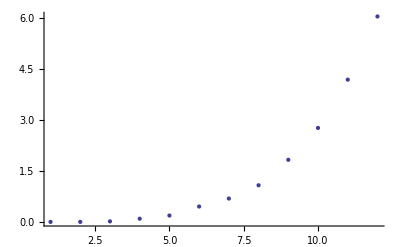

```mathematica
ListPlot@%[[All,1]]
```

Due to the part b_, c___, d_ the above rule has to test many possible cases. A simpler rule should be  to compare only neighboring elements:

```mathematica
rule2={a___,b_,d_,e___}:>{a,d,b,e}/;d<b
```

{a___,b_,d_,e___}:>{a,d,b,e}/;d<b

```mathematica
AbsoluteTiming[ReplaceRepeated[#,rule2]]&/@Table[Range[5*i]//Reverse,{i,1,25}]
```

{{0.,{1,2,3,4,5}},{0.,{1,2,3,4,5,6,7,8,9,10}},{0.,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}},{0.,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}},{0.0156,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}},{0.0156,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}},{0.0312,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35}},{0.0312,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40}},{0.0624,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}},{0.078,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}},{0.0936,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55}},{0.1404,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60}},{0.1716,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}},{0.234,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70}},{0.2808,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75}},{0.3588,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80}},{0.4212,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85}},{0.5148,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90}},{0.624,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95}},{0.7488,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}},{0.858,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105}},{0.9984,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110}},{1.1856,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115}},{1.3884,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120}},{1.6536,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125}}}

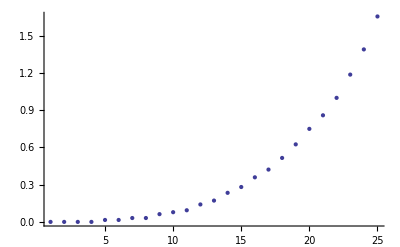

```mathematica
ListPlot[%[[All,1]]]
```

The second rule seems to be faster for a reversed list.

### Excercise

Try the two sorting rules on different test lists. Do they behave or scale differently on different cases? Can you find an example where rule1 is faster than rule2? Under which circumstances do the rules fail or give different results?

## Rules & Patterns - continuation

### String Patterns

Required Reading:

String Patterns Tutorial
String Patterns Guide
Working with String Patterns

A string in Mathematica is enclosed in quotes. Patterns are not part of a string, but of a StringExpression. 
s_1~~s_2~~… or StringExpression[s_1,s_2,…]represents a sequence of strings and symbolic string objects s_i.

A string expression representing the string "ab" followed by any single character:

```mathematica
"ab" ~~ _
```

ab~~_

This makes a replacement for each occurrence of the string pattern "ab"~~__:

```mathematica
StringReplace["abc abcb abdc","ab"~~_->"X"]
```

X Xb Xc

If consecutive elements in a string expression are strings, then they are automatically concatenated to one string. Here is an example of this situation.

```mathematica
StringExpression["1", 2]
```

1~~2

```mathematica
StringExpression["1", "2", 3]
```

12~~3

Let's look at all built-in functions having the name String… and having nonstring analog. Here is a list of these functions.

```mathematica
Select[Names["String*"], MemberQ[Names["*"], StringDrop[#, 6]]&]
```

{StringBreak,StringByteCount,StringCases,StringCount,StringDrop,StringExpression,StringFormat,StringFreeQ,StringInsert,StringJoin,StringLength,StringMatchQ,StringPosition,StringReplace,StringReplaceList,StringReplacePart,StringReverse,StringSkeleton,StringSplit,StringTake}

To find out if a given string matches a given pattern, the function StringMatchQ can be used.

```mathematica
StringMatchQ["123456789", "1" ~~ _ ~~ "9"]
```

False

```mathematica
StringMatchQ["123456789", "1" ~~ __ ~~ "9"]
```

True

Here are some possibilities to match any string of length two or larger.

```mathematica
StringMatchQ["abc", StringExpression[__]]
```

True

```mathematica
StringMatchQ["abc", StringExpression[_ ..]]
```

True

Here we used the Repeated (..)operator. p.. or Repeated[p]is a pattern object which represents a sequence of one or more expressions, each matching p.

If you want to check that a string is free of "a" use StringFreeQ:

```mathematica
StringFreeQ["abcd","a"]
```

False

Find the starting and ending positions at which XYZ occurs in a string use StringPosition["string","sub"]

```mathematica
StringPosition["abXYZaaabXYZaaaaXYZXYZ","XYZ"]
```

{{3,5},{10,12},{17,19},{20,22}}

The next input determines the string position of a substring that begins with the substring "1" and is followed by at least one more character.

```mathematica
StringPosition["12345678987654321", "12" ~~ __]
```

{{1,17}}

The last call to StringPosition returned the whole string—the longest possible match. To obtain the shortest possible match, we can use the function ShortestMatch.

```mathematica
StringPosition["12345678987654321", ShortestMatch["12" ~~ __]]
```

{{1,3}}

```mathematica
StringReplace["123456789", x:__:> "X"]
```

X

The above result again was the longest possible match. All possible matches are given by StringReplaceList

```mathematica
StringReplaceList["123456789", x:__:> "X"]
```

{X,X9,X89,X789,X6789,X56789,X456789,X3456789,X23456789,1X,1X9,1X89,1X789,1X6789,1X56789,1X456789,1X3456789,12X,12X9,12X89,12X789,12X6789,12X56789,12X456789,123X,123X9,123X89,123X789,123X6789,123X56789,1234X,1234X9,1234X89,1234X789,1234X6789,12345X,12345X9,12345X89,12345X789,123456X,123456X9,123456X89,1234567X,1234567X9,12345678X}

### Regular Expressions

Required Reading

Regular Expressions

You may sometimes find it convenient to specify string patterns using regular expression notation. You can do this in Mathematica with RegularExpression objects.  RegularExpression["regex"]represents the generalized regular expression specified by the string "regex".

Find words involving the characters a, b, c, d, e:

```mathematica
StringCases["adefgh12c34",RegularExpression["[a-e]+"]]
```

{ade,c}

Equivalent form using string patterns :

```mathematica
StringCases["adefgh12c34",CharacterRange["a","e"]..]
```

{ade,c}

Decide whether the string consists of words and whitespace:

```mathematica
StringMatchQ["abcd\nefgh\n1234",RegularExpression["(\\w|\\s)*"]]
```

True

Equivalent form using string patterns:

```mathematica
StringMatchQ["abcd\nefgh\n1234",(WordCharacter|Whitespace)...]
```

True

Numbered subpatterns:

```mathematica
StringCases["a1b6a3b3a3c3a8b8",RegularExpression["(a(\\d))b\\2"]->{"$0","$1","$2"}]
```

{{a3b3,a3,3},{a8b8,a8,8}}

#### Example: Poor mans encryption

In the shift cipher, each character is represented by a number and then a fixed number (the key) is added to all the characters to form the cipher text. For simplicity, we remove all spaces and punctuation from the text and assume that every character is a lower case letter.

We will convert a string to its character code and then add the constant number to it and then convert is back to the character code.

```mathematica
ToCharacterCode["abcdefghijklmnopqrstuvwxyz"]
```

{97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122}

We see that the codes are consecutive. This will make the computation simpler. If we subtract 97 from the code, and then add number modulo 26, then add 97 to the number and convert it back to a string, then we will have the cipher text.

```mathematica
"Let us encrypt this text"
```

Let us encrypt this text

```mathematica
StringReplace[ToLowerCase[%],{" "->""}]
```

letusencryptthistext

```mathematica
ToCharacterCode[%]-97
```

{11,4,19,20,18,4,13,2,17,24,15,19,19,7,8,18,19,4,23,19}

Now we add the key to the character code. We chose 11:

```mathematica
Mod[%+12,26]
```

{23,16,5,6,4,16,25,14,3,10,1,5,5,19,20,4,5,16,9,5}

```mathematica
FromCharacterCode[%+97]
```

xqfgeqzodkbfftuefqjf

Excercise: try to decrypt the following: "kyzjzjrcfexvijvekvetvkyrkyrjsvvevetipgkvu"

#### Example: Highligh Patterns

This defines a 1000-base random DNA string.

```mathematica
SeedRandom[1234];dna=StringJoin[Table[{"a","c","g","t"}[[RandomInteger[{1,4}]]],{1000}]]
```

tgaacggccgggaactaaaagacacagaccgcttctagttgacataccgacgaccgacaggttcaatgtgggtaatcgcgaagttgtgctcaatctgccgcgttaaagttgtagatgacaaccaagtacatgtccgacccaagtcgattcttagcggagtatatggcagtgtaagagcccgactgggtccctggttgagctcgtgcgcattgtattatcatttccggggtttcctaaggagagagtccgtacacctcagctttaaggagaaacactattctgcgccatctgcaacacatgagtctgttagcactccgaagagcgcttgagccagggaatgagcttcgctacctccgctgtaagtgcccctctctgcctctttccaacctccaatgcatgttgtcgccgttagccagtggtcggacagtctgaaatgttagcacgtagaaactctacccattacggccatttagtttaatgtcaacaatgtagctgccggaatcggattaacactcgcgaaacccataggtatgcccaccactgctctaggcagtgaacgagggttcacgactgtagatctctgatagcctcaaccccgtaaactggcatgatcccgatgctgctcgcgtagttgtgactattttaaactaggacttgtcccataaacatccccgcctcataagtgagacatcagcatgagtgacgtaacagattgattttgggcgcatctgaggcagcggcttaattcgtgcctcattcctaagaagacggggtattaattagaagcaatagcgctttgccgagccatctcgattgccagtccctcacatttatcgaggtgctgaagctgtggagggatgacactgtggctcctttgcaatcctcggacttagatcacactagccgctgcggtcgttcgtgagcgaccccgctcagtcgtagcccacgggaattgtcagcttaaagaaaaccgtgatctgtaaccaccggcgtctactcg

This highlights parts of the DNA that match a certain pattern.

```mathematica
StringReplace[dna,x:("ag"~~_~~_~~"t"~~_~~"ca"):>"\!\(\*StyleBox[\""<>x<>"\",FontColor->RGBColor[1,0,0],FontSize->18,FontWeight->\"Bold\"]\)"]
```

tgaacggccgggaactaaaagacacagaccgcttctagttgacataccgacgaccgacaggttcaatgtgggtaatcgcgaagttgtgctcaatctgccgcgttaaagttgtagatgacaaccaagtacatgtccgacccaagtcgattcttagcggagtatatggcagtgtaagagcccgactgggtccctggttgagctcgtgcgcattgtattatcatttccggggtttcctaaggagagagtccgtacacctcagctttaaggagaaacactattctgcgccatctgcaacacatgagtctgttagcactccgaagagcgcttgagccagggaatgagcttcgctacctccgctgtaagtgcccctctctgcctctttccaacctccaatgcatgttgtcgccgttagccagtggtcggacagtctgaaatgttagcacgtagaaactctacccattacggccatttagtttaatgtcaacaatgtagctgccggaatcggattaacactcgcgaaacccataggtatgcccaccactgctctaggcagtgaacgagggttcacgactgtagatctctgatagcctcaaccccgtaaactggcatgatcccgatgctgctcgcgtagttgtgactattttaaactaggacttgtcccataaacatccccgcctcataagtgagacatcagcatgagtgacgtaacagattgattttgggcgcatctgaggcagcggcttaattcgtgcctcattcctaagaagacggggtattaattagaagcaatagcgctttgccgagccatctcgattgccagtccctcacatttatcgaggtgctgaagctgtggagggatgacactgtggctcctttgcaatcctcggacttagatcacactagccgctgcggtcgttcgtgagcgaccccgctcagtcgtagcccacgggaattgtcagcttaaagaaaaccgtgatctgtaaccaccggcgtctactcg

Here is the same result using a regular expression.

```mathematica
StringReplace[dna,RegularExpression["ag..t.ca"]:>"\!\(\*StyleBox[\"$0\",FontColor->RGBColor[1,0,0],FontSize->18,FontWeight->\"Bold\"]\)"]
```

tgaacggccgggaactaaaagacacagaccgcttctagttgacataccgacgaccgacaggttcaatgtgggtaatcgcgaagttgtgctcaatctgccgcgttaaagttgtagatgacaaccaagtacatgtccgacccaagtcgattcttagcggagtatatggcagtgtaagagcccgactgggtccctggttgagctcgtgcgcattgtattatcatttccggggtttcctaaggagagagtccgtacacctcagctttaaggagaaacactattctgcgccatctgcaacacatgagtctgttagcactccgaagagcgcttgagccagggaatgagcttcgctacctccgctgtaagtgcccctctctgcctctttccaacctccaatgcatgttgtcgccgttagccagtggtcggacagtctgaaatgttagcacgtagaaactctacccattacggccatttagtttaatgtcaacaatgtagctgccggaatcggattaacactcgcgaaacccataggtatgcccaccactgctctaggcagtgaacgagggttcacgactgtagatctctgatagcctcaaccccgtaaactggcatgatcccgatgctgctcgcgtagttgtgactattttaaactaggacttgtcccataaacatccccgcctcataagtgagacatcagcatgagtgacgtaacagattgattttgggcgcatctgaggcagcggcttaattcgtgcctcattcctaagaagacggggtattaattagaagcaatagcgctttgccgagccatctcgattgccagtccctcacatttatcgaggtgctgaagctgtggagggatgacactgtggctcctttgcaatcctcggacttagatcacactagccgctgcggtcgttcgtgagcgaccccgctcagtcgtagcccacgggaattgtcagcttaaagaaaaccgtgatctgtaaccaccggcgtctactcg

#### Excercise

Assume you have a text (file) with the following structure:

blah blah

BEGINIGNORE
this stuff should get stripped out
ENDIGNORE

more stuff here

To strip out everything between BEGINIGNORE and ENDIGNORE, inclusive in e.g. perl the syntax would be:  s/BEGINIGNORE.*ENDIGNORE//s

How would You do that in Mathematica?

### Working with Strings: Text Analysis

Taken from Professor Brian G. Higgins, UC Davis.

We want to demonstrate some of the text capailities of Mathematica. Let's start with an example text

```mathematica
text = Import["ExampleData/USConstitution.txt"];
```

This is a long string

```mathematica
Short[text]
```

We the People of the United St…ntatives shall
have intervened.

To split it up into a list of its words we us StringSplit.

```mathematica
wordlist=StringSplit[text, RegularExpression["\s"]];
```

\s stands for any whitespace character. This does not get rid of any periods, commas, etc.:

```mathematica
wordlist[[1;;20]]//FullForm
```

List["We","the","People","of","the","United","States,","in","Order","to","form","a","more","perfect","Union,","establish","Justice,","insure","domestic","Tranquility,"]

To remove all non-word characters we pull out all letters:

```mathematica
words=Flatten[StringCases[wordlist,RegularExpression["([a-zA-Z]+)"]]];
```

We could try a different approach. If we ask StringSplit to also split around non-word characters \W we get a better list of words

```mathematica
wordlist2=StringSplit[text, RegularExpression["\s|\W"]];
```

```mathematica
wordlist2[[1;;20]]//FullForm
```

List["We","the","People","of","the","United","States","","in","Order","to","form","a","more","perfect","Union","","establish","Justice",""]

No more dots around, but superfluous empty characters "".

```mathematica
words2=Flatten[DeleteCases[wordlist2,""|DigitCharacter]];
```

Let's ask Mathematica if the two sets are identical:

```mathematica
words==words2
```

False

```mathematica
Length/@{words,words2}
```

Where does the difference come from? A closer look at the both lists position for position reveals the difference:

```mathematica
Table[{words[[i]],words2[[i]]},{i,1,5000}][[1;;60]]
```

{{We,We},{the,the},{People,People},{of,of},{the,the},{United,United},{States,States},{in,in},{Order,Order},{to,to},{form,form},{a,a},{more,more},{perfect,perfect},{Union,Union},{establish,establish},{Justice,Justice},{insure,insure},{domestic,domestic},{Tranquility,Tranquility},{provide,provide},{for,for},{the,the},{common,common},{defence,defence},{promote,promote},{the,the},{general,general},{Welfare,Welfare},{and,and},{secure,secure},{the,the},{Blessings,Blessings},{of,of},{Liberty,Liberty},{to,to},{ourselves,ourselves},{and,and},{our,our},{Posterity,Posterity},{do,do},{ordain,ordain},{and,and},{establish,establish},{this,this},{Constitution,Constitution},{for,for},{the,the},{United,United},{States,States},{of,of},{America,America},{Article,Article},{I,I},{Section,Section},{All,1},{legislative,All},{Powers,legislative},{herein,Powers},{granted,herein}}

Obviously we didn't filter out the section numbers and ordinal numbers

```mathematica
Complement[words2,words]
```

{1,10,15th,2,20th,3,3d,4,5,6,7,8,9}

On the other hand our first list contains some weird relics

```mathematica
Complement[words,words2]
```

{d,th}

Using the same approach we can easily extract all numbers from the text

```mathematica
numbers=Flatten[StringCases[wordlist,RegularExpression["([0-9]+)"]]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,1,2,3,1,2,3,4,1,2,1,2,3,4,5,1,2,1,2,3,1,20,3,2,3,3,4,5,1,2,15,6,1,2,3,1,2,1,2,1,2,1,2,3,4,1,2}

They are also still part of the second word list

```mathematica
numbers=Flatten[StringCases[words2,RegularExpression["([0-9]+)"]]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,1,2,3,1,2,3,4,1,2,1,2,3,4,5,1,2,1,2,3,1,20,3,2,3,3,4,5,1,2,15,6,1,2,3,1,2,1,2,1,2,1,2,3,4,1,2}

The equivalent Mathematica pattern to do this is:

```mathematica
Flatten[StringCases[wordlist,NumberString]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,1,2,3,1,2,3,4,1.,2.,1.,2.,3.,4.,5.,1.,2.,1.,2.,3.,1.,20,3,2.,3,3.,4.,5.,1,2,15,6.,1.,2.,3.,1.,2.,1.,2.,1.,2.,1.,2.,3.,4.,1.,2.}

Next, we take a closer look at the words:

```mathematica
sortedWords=Sort[words];
```

```mathematica
sortedWords[[1;;500]]
```

{a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,A,A,A,Ability,Abr,abridge,abridged,abridged,abridged,abridged,abridged,abridging,absence,absent,absolutely,accept,acceptance,according,according,according,according,according,according,accordingly,accordingly,account,account,account,Account,accusation,accused,act,act,act,act,act,act,act,Act,acted,acting,acting,Acting,Acting,Acting,Acts,Acts,actual,actual,actual,actually,adding,addition,adhering,adjourn,adjourn,adjourn,Adjournment,Adjournment,Adjournment,admiralty,admit,admit,admitted,Adoption,Adoption,Advice,Advice,affect,affect,affecting,affecting,affirm,affirmation,Affirmation,Affirmation,Affirmation,after,after,after,after,after,after,after,After,against,against,against,against,against,against,against,against,against,against,against,against,against,against,age,age,age,age,Age,Age,Age,agree,Agreement,aid,aid,Aid,Alexander,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,all,All,All,All,All,Alliance,alone,also,alter,Ambassadors,Ambassadors,Ambassadors,Ambassadors,amendment,amendment,amendment,amendment,amendment,amendment,amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendment,Amendments,Amendments,Amendments,America,America,America,among,among,among,among,an,an,an,an,an,an,an,an,an,an,an,an,an,an,an,an,an,an,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and,and}

If we want to do statistics on the individual words we can use many approaches. We could use Tally to have a quick count:

```mathematica
Tally[sortedWords]
```

{{a,94},{A,3},{Ability,1},{Abr,1},{abridge,1},{abridged,5},{abridging,1},{absence,1},{absent,1},{absolutely,1},{accept,1},{acceptance,1},{according,6},{accordingly,2},{account,3},{Account,1},{accusation,1},{accused,1},{act,7},{Act,1},{acted,1},{acting,2},{Acting,3},{Acts,2},{actual,3},{actually,1},{adding,1},{addition,1},{adhering,1},{adjourn,3},{Adjournment,3},{admiralty,1},{admit,2},{admitted,1},{Adoption,2},{Advice,2},{affect,2},{affecting,2},{affirm,1},{affirmation,1},{Affirmation,3},{after,7},{After,1},{against,14},{age,4},{Age,3},{agree,1},{Agreement,1},{aid,2},{Aid,1},{Alexander,1},{all,37},{All,4},{Alliance,1},{alone,1},{also,1},{alter,1},{Ambassadors,4},{amendment,7},{Amendment,28},{Amendments,3},{America,3},{among,4},{an,18},{and,258},{And,6},{another,7},{answer,1},{any,79},{appellate,1},{Application,2},{apply,1},{appoint,5},{appointed,7},{Appointment,2},{appointments,1},{Appointments,2},{apportioned,2},{apportionment,1},{appropriate,8},{Appropriation,1},{Appropriations,1},{approve,1},{approved,2},{are,4},{arising,2},{Armies,1},{arming,1},{Arms,1},{Army,1},{Arrest,1},{Arsenals,1},{article,17},{Article,11},{Articles,1},{Arts,1},{as,64},{ascertained,2},{assemble,4},{assembled,1},{assembling,1},{Assistance,1},{assume,2},{at,23},{Attainder,3},{attained,3},{attainted,1},{Attendance,2},{Attest,1},{authority,1},{Authority,7},{authorized,2},{Authors,1},{B,1},{bail,1},{Baldwin,1},{ballot,2},{Ballot,3},{ballots,2},{Bankruptcies,1},{basis,1},{Bassett,1},{be,179},{bear,2},{become,5},{becomes,2},{Bedford,1},{been,17},{before,9},{Before,1},{begin,2},{beginning,2},{Behavior,2},{being,3},{belonging,1},{best,1},{between,7},{beverage,1},{Bill,7},{bills,1},{Bills,2},{Blair,1},{Blessings,1},{Blood,1},{Blount,1},{body,2},{born,2},{borrow,1},{both,9},{bound,4},{bounties,1},{branch,1},{Branch,1},{Breach,1},{Brearley,1},{Bribery,1},{Broom,1},{Buildings,1},{Business,1},{but,23},{But,10},{Butler,1},{by,100},{call,1},{called,1},{calling,1},{cannot,1},{capital,1},{capitation,1},{Captures,1},{Care,1},{Carolina,4},{Carroll,1},{carrying,1},{case,6},{Case,7},{cases,1},{Cases,12},{cause,2},{census,1},{Census,1},{certain,1},{certificates,1},{Certificates,1},{certify,2},{Cession,1},{charged,1},{Charles,2},{Chief,2},{choice,6},{Choice,2},{choose,5},{choosing,1},{chosen,8},{chuse,6},{chusing,2},{Chusing,1},{Citizen,4},{citizens,9},{Citizens,9},{civil,3},{claim,1},{Claim,1},{claiming,1},{claims,1},{Claims,1},{Class,3},{Classes,1},{Clauses,1},{clear,1},{Clymer,1},{coin,2},{Coin,3},{collect,2},{color,1},{comfort,1},{Comfort,1},{Commander,1},{commenced,1},{Commerce,2},{Commission,1},{Commissions,1},{committed,4},{common,4},{Compact,1},{compel,1},{compelled,1},{compensation,2},{Compensation,3},{composed,3},{compulsory,1},{concerned,1},{concerning,1},{concur,2},{Concurrence,3},{concurrent,1},{condition,1},{Confederation,2},{Confession,1},{confirmation,1},{confronted,1},{Congress,60},{Connecticut,2},{consent,1},{Consent,10},{Consequence,3},{Consideration,1},{considered,1},{consist,5},{constitute,2},{constituting,1},{Constitution,25},{constitutional,1},{constitutionally,1},{construed,4},{Consuls,3},{Continuance,2},{continue,1},{contracted,1},{Contracts,1},{contrary,1},{Contrary,1},{Controul,1},{Controversies,2},{controversy,1},{convene,1},{convened,1},{Convention,2},{conventions,1},{Conventions,2},{convicted,4},{Conviction,1},{Corpus,1},{Corruption,1},{Cotesworth,1},{Counsel,1},{counted,2},{counterfeiting,1},{counting,1},{Court,7},{Courts,3},{created,1},{credit,1},{Credit,2},{crime,4},{Crime,2},{Crimes,3},{criminal,2},{cruel,1},{current,1},{d,2},{Dan,1},{danger,1},{Danger,1},{Danl,1},{date,4},{David,1},{day,8},{Day,4},{days,4},{Days,1},{Dayton,1},{death,4},{Death,2},{Debate,1},{debt,2},{debts,2},{Debts,3},{December,1},{decide,1},{declaration,6},{declare,2},{declaring,2},{deem,1},{defence,2},{Defence,1},{defend,1},{define,1},{Delaware,2},{delay,1},{delegated,1},{delivered,2},{delivery,1},{demand,1},{denied,5},{deny,2},{department,1},{Department,1},{departments,1},{Departments,2},{deprive,1},{deprived,2},{deputy,1},{derived,1},{describing,1},{Desire,1},{determine,2},{determined,2},{determines,1},{devolve,2},{devolved,2},{Dickinson,1},{died,1},{different,4},{diminished,2},{direct,6},{directed,4},{disability,2},{Disability,1},{Disagreement,1},{disapproved,1},{discharge,6},{discharged,2},{discipline,1},{disciplining,1},{Discoveries,1},{disorderly,1},{disparage,1},{dispose,1},{disqualification,1},{distinct,2},{district,2},{District,4},{divided,2},{do,3},{Dobbs,1},{dock,1},{dollars,2},{domestic,2},{Done,1},{drawn,1},{due,3},{duly,1},{during,14},{duties,9},{Duties,7},{duty,2},{Duty,1},{each,22},{Each,4},{effect,2},{Effect,2},{effects,1},{eight,7},{eighteen,1},{eighteenth,1},{Eighty,1},{either,7},{elect,6},{elected,10},{election,7},{Election,2},{Elections,2},{elector,1},{Elector,1},{electors,6},{Electors,10},{eligible,3},{emancipation,1},{emit,1},{Emolument,2},{Emoluments,1},{employed,1},{empower,1},{end,1},{End,1},{ended,1},{enemies,1},{Enemies,1},{enforce,9},{engage,1},{engaged,1},{Engagements,1},{enjoy,2},{enter,5},{entered,3},{entitled,4},{enumeration,3},{Enumeration,2},{equal,6},{equally,2},{equity,1},{Equity,1},{erected,1},{Erection,1},{escaping,1},{establish,5},{established,1},{establishment,1},{Establishment,1},{event,1},{ever,1},{every,10},{Every,2},{ex,2},{examined,1},{exceed,2},{exceeding,3},{except,11},{excepted,1},{excepting,1},{Exceptions,1},{excessive,1},{Excessive,1},{Excises,2},{excluding,2},{exclusive,2},{execute,2},{executed,1},{executing,1},{Execution,2},{executive,9},{Executive,4},{exercise,4},{exist,1},{existing,1},{exists,1},{expedient,1},{expel,1},{Expenditures,1},{Expiration,3},{expire,1},{exportation,1},{exported,1},{Exports,2},{extend,3},{extraordinary,1},{fact,1},{Fact,1},{facto,2},{failed,1},{failure,1},{Faith,1},{faithfully,2},{favor,1},{Felonies,1},{Felony,2},{Few,1},{fifth,1},{fifths,1},{fill,5},{fines,1},{first,6},{FitzSimons,1},{five,6},{fix,1},{fixed,2},{fled,1},{flee,1},{following,3},{follows,1},{for,84},{forces,1},{Forces,1},{foregoing,1},{foreign,5},{Foreign,1},{Forfeiture,1},{form,1},{Form,1},{formed,2},{forth,1},{Forts,1},{forty,1},{found,1},{four,3},{fourteen,1},{fourth,3},{fourths,4},{Franklin,1},{free,3},{freedom,1},{from,41},{Full,1},{further,1},{general,3},{Geo,2},{Georgia,2},{Gilman,1},{give,2},{given,3},{giving,1},{Go,1},{going,1},{gold,1},{good,1},{Gorham,1},{Gouv,1},{governing,1},{government,1},{Government,7},{Grand,1},{grant,3},{Grant,1},{granted,2},{granting,1},{Grants,1},{greatest,4},{grievances,1},{guarantee,1},{Gunning,1},{Habeas,1},{had,2},{Hamilton,1},{Hampshire,2},{happen,4},{has,1},{have,63},{having,9},{he,25},{He,3},{Heads,1},{held,5},{hereby,3},{herein,3},{hereof,2},{hereunto,1},{high,2},{highest,3},{him,4},{himself,1},{his,18},{hold,4},{holding,7},{honor,1},{hours,1},{house,1},{House,32},{houses,1},{Houses,7},{Hu,1},{hundred,3},{I,4},{if,18},{If,6},{II,2},{III,2},{illegal,1},{immediately,3},{Immediately,1},{imminent,1},{immunities,1},{Immunities,1},{impairing,1},{impartial,1},{Impeachment,5},{Impeachments,1},{importation,2},{Importation,2},{Imports,2},{imposed,2},{Imposts,4},{in,137},{In,8},{inability,1},{Inability,2},{included,1},{including,2},{incomes,1},{increased,2},{incurred,2},{Independence,1},{Indian,1},{Indians,2},{indictment,1},{Indictment,1},{ineligible,1},{infamous,1},{inferior,4},{inflicted,1},{Information,1},{informed,1},{infringed,1},{Ingersoll,1},{inhabitant,1},{Inhabitant,3},{inhabitants,1},{inoperative,4},{inspection,1},{insure,1},{insurrection,3},{Insurrections,1},{Intents,1},{intervened,1},{into,10},{intoxicating,2},{invaded,1},{Invasion,2},{Invasions,1},{Inventors,1},{involuntary,1},{is,13},{Island,1},{issue,4},{it,21},{its,10},{IV,2},{IX,1},{J,1},{Jackson,1},{Jaco,1},{James,3},{January,3},{Jared,1},{Jenifer,1},{jeopardy,1},{Jersey,2},{John,3},{Johnson,1},{Jona,1},{Journal,4},{Jr,1},{judge,1},{Judge,1},{Judges,3},{Judgment,3},{judicial,5},{Judicial,2},{jun,1},{Junction,1},{jurisdiction,4},{Jurisdiction,5},{jury,3},{Jury,2},{just,1},{Justice,3},{keep,3},{kind,1},{King,2},{Labour,3},{laid,3},{land,2},{Land,2},{Lands,1},{Langdon,1},{large,1},{latter,1},{law,16},{Law,23},{laws,2},{Laws,11},{lay,4},{least,5},{Least,1},{legislation,8},{Legislation,1},{legislative,1},{legislature,3},{Legislature,10},{legislatures,4},{Legislatures,4},{Letters,2},{levying,1},{liable,1},{liberty,2},{Liberty,1},{lie,1},{life,3},{Life,1},{like,3},{likewise,1},{limb,1},{Limitations,1},{limited,1},{liquors,2},{list,2},{List,3},{lists,2},{Livingston,1},{longer,1},{Lord,1},{loss,1},{made,9},{Madison,1},{Magazines,1},{maintain,1},{majority,9},{Majority,5},{make,14},{male,3},{manner,3},{Manner,8},{manufacture,1},{March,1},{maritime,1},{Marque,2},{Maryland,2},{Massachusetts,2},{may,44},{McHenry,1},{Measures,2},{meet,3},{meeting,1},{Meeting,3},{member,3},{Member,3},{members,2},{Members,8},{mentioned,2},{Mifflin,1},{Migration,1},{Miles,1},{military,1},{Militia,6},{Ministers,4},{Misdemeanors,1},{Mode,1},{Monday,1},{money,1},{Money,5},{more,10},{Morris,2},{most,2},{my,1},{name,1},{Names,2},{Nathaniel,1},{Nations,2},{natural,1},{Naturalization,1},{naturalized,1},{nature,1},{naval,2},{Navy,2},{Nays,2},{necessary,9},{needful,2},{neither,4},{Neither,2},{net,1},{nevertheless,1},{new,1},{New,7},{next,3},{Nicholas,1},{nine,2},{Ninth,1},{no,21},{No,21},{Nobility,2},{nominate,2},{noon,3},{nor,17},{North,2},{not,44},{nothing,1},{notwithstanding,1},{now,1},{number,14},{Number,11},{numbers,3},{Numbers,1},{numerous,2},{oath,1},{Oath,4},{Objections,3},{obligation,1},{Obligation,1},{obligations,1},{obliged,1},{obtaining,1},{Occasions,1},{October,1},{of,494},{offense,1},{Offenses,2},{office,18},{Office,19},{officer,2},{Officer,4},{officers,3},{Officers,8},{Offices,3},{older,1},{on,39},{once,3},{one,28},{One,1},{only,1},{open,3},{operative,1},{Opinion,1},{or,160},{ordain,2},{Order,2},{organizing,1},{original,1},{originate,1},{originated,1},{other,31},{others,1},{otherwise,5},{our,3},{ourselves,1},{out,1},{over,3},{overt,1},{own,1},{Owner,1},{paid,1},{papers,1},{Pardons,1},{part,2},{Part,1},{participation,1},{particular,2},{particularly,1},{parts,1},{Parts,1},{party,1},{Party,4},{pass,2},{passed,2},{Paterson,1},{pay,4},{payment,1},{Payment,1},{peace,1},{Peace,2},{peaceably,1},{Penalties,1},{Pennsylvania,1},{pensions,1},{Pensylvania,1},{people,7},{People,2},{perfect,1},{perform,1},{Period,2},{person,20},{Person,14},{persons,10},{Persons,5},{petition,1},{Pierce,1},{Pinckney,2},{Piracies,1},{place,2},{Place,4},{Places,3},{Plantations,1},{poll,1},{populous,1},{Ports,1},{possession,1},{post,2},{Post,2},{Posterity,1},{power,11},{Power,11},{powers,9},{Powers,4},{Preference,1},{Prejudice,1},{prescribe,1},{prescribed,4},{presence,1},{Presence,1},{present,4},{Present,1},{presented,3},{presentment,1},{preserve,1},{preserved,1},{preside,1},{President,121},{press,1},{prevent,2},{previous,1},{previously,2},{primary,1},{Prince,1},{principal,3},{prior,2},{private,1},{privilege,1},{privileged,1},{privileges,1},{Privileges,1},{pro,5},{probable,1},{proceed,1},{Proceedings,4},{process,3},{Produce,1},{Profit,3},{Progress,1},{prohibited,4},{prohibiting,1},{promote,2},{proper,4},{property,3},{Property,1},{proportion,1},{Proportion,1},{propose,2},{proposed,2},{proposing,1},{prosecuted,1},{prosecutions,1},{protect,2},{protection,1},{proved,1},{provide,12},{provided,5},{Provided,2},{Providence,1},{provisions,1},{public,12},{publish,1},{published,1},{punish,2},{punishment,1},{Punishment,3},{punishments,1},{purchased,1},{purpose,3},{Purpose,2},{purposes,2},{Purposes,1},{Pursuance,1},{put,1},{Qualification,1},{qualifications,1},{Qualifications,2},{qualified,3},{qualify,1},{quartered,1},{question,2},{questioned,2},{quorum,3},{Quorum,1},{race,1},{raise,1},{raising,1},{ratification,2},{Ratification,2},{ratified,6},{ratifying,1},{re,1},{Read,1},{reason,1},{rebellion,4},{Rebellion,1},{receipt,1},{Receipts,1},{receive,5},{Recess,2},{recommend,1},{reconsider,1},{Reconsideration,1},{reconsidered,1},{Records,2},{redress,1},{reduced,1},{regard,1},{regular,1},{regulate,2},{regulated,1},{Regulation,3},{Regulations,3},{relating,1},{religion,1},{religious,1},{remain,1},{remainder,1},{removal,2},{Removal,2},{remove,1},{removed,3},{repassed,1},{repealed,1},{repel,1},{representation,3},{Representation,2},{Representative,6},{Representatives,29},{Reprieves,1},{Reprisal,2},{Republican,1},{require,3},{required,3},{requisite,2},{reserved,1},{reserving,1},{reside,1},{Resident,1},{resignation,1},{Resignation,3},{Resolution,1},{Respect,1},{respecting,2},{respective,7},{respectively,3},{resume,2},{retained,1},{return,1},{Return,1},{returned,1},{returning,1},{Returns,1},{Revenue,2},{Revision,1},{Rhode,1},{Richard,1},{Richd,1},{right,13},{Right,1},{rights,1},{Roads,1},{Robt,1},{Roger,1},{Rufus,1},{Rule,1},{rules,1},{Rules,5},{Rutledge,1},{s,1},{Safety,1},{said,3},{sale,1},{same,12},{Same,4},{Saml,1},{Science,1},{sealed,2},{searched,1},{searches,1},{Seas,1},{seat,2},{Seat,2},{Seats,1},{second,4},{Secrecy,1},{Secretary,1},{Section,22},{Sections,1},{secure,2},{securing,1},{Securities,1},{security,1},{seized,1},{seizures,1},{selected,1},{Senate,28},{Senator,8},{Senators,13},{sent,1},{September,1},{service,1},{Service,6},{services,2},{Services,3},{servitude,2},{session,2},{Session,3},{seven,7},{Seventeenth,1},{several,16},{sex,1},{shall,306},{Sherman,1},{Ships,1},{should,1},{sign,3},{signed,1},{silver,1},{sitting,2},{six,4},{sixth,1},{slave,1},{slavery,1},{smaller,1},{so,4},{Soldier,1},{sole,2},{solemnly,1},{some,1},{source,1},{South,2},{Spaight,1},{Speaker,5},{speech,1},{Speech,1},{speedy,1},{square,1},{St,1},{Standard,1},{state,2},{State,77},{stated,2},{Statement,1},{states,4},{States,125},{subject,8},{Subjects,2},{submission,4},{subscribed,1},{subsequent,1},{successors,1},{such,52},{sufficient,1},{Suffrage,1},{suit,1},{Suits,1},{Sundays,1},{support,3},{supported,1},{suppress,1},{suppressing,1},{supreme,7},{suspended,1},{swear,1},{take,6},{taken,5},{tax,3},{Tax,2},{taxed,2},{taxes,1},{Taxes,2},{temporary,2},{tempore,5},{ten,5},{Tender,1},{term,6},{Term,5},{terms,4},{territory,1},{Territory,2},{Test,1},{Testimony,1},{th,2},{than,10},{that,23},{That,1},{the,662},{The,64},{their,28},{them,15},{themselves,2},{then,12},{there,3},{Thereafter,1},{thereby,1},{therein,3},{thereof,22},{Thereupon,1},{they,19},{They,1},{Thing,2},{things,1},{think,3},{third,2},{thirds,13},{thirty,3},{this,30},{This,5},{Tho,1},{Thomas,1},{Thos,1},{those,6},{thousand,3},{Thousand,1},{three,11},{throughout,3},{time,17},{Time,4},{Times,4},{Title,3},{to,184},{To,18},{together,2},{Tonnage,1},{training,1},{Tranquility,1},{transmit,4},{transmits,3},{transportation,2},{Treason,7},{Treasury,3},{Treaties,3},{Treaty,1},{trial,2},{Trial,4},{Tribes,1},{Tribunals,1},{tried,2},{Troops,1},{Trust,4},{try,1},{twelfth,1},{Twelfth,1},{twenty,6},{twice,2},{two,24},{unable,4},{Unanimous,1},{under,17},{uniform,3},{Union,6},{United,85},{unless,14},{unreasonable,1},{until,8},{unusual,1},{up,3},{upon,6},{use,2},{Use,2},{useful,1},{V,2},{vacancies,4},{Vacancies,4},{vacancy,1},{vacated,1},{valid,3},{validity,1},{value,1},{Value,1},{varying,1},{Vessels,1},{vest,1},{vested,4},{VI,2},{Vice,36},{VII,2},{VIII,1},{violated,1},{violation,1},{Violence,1},{Virginia,3},{void,1},{vote,12},{Vote,4},{voted,6},{votes,5},{Votes,9},{voting,1},{war,1},{War,5},{Warrants,1},{was,3},{Washington,1},{Water,1},{way,1},{We,2},{Weights,1},{Welfare,2},{well,2},{were,1},{what,2},{whatever,2},{whatsoever,1},{when,12},{When,4},{whenever,4},{Whenever,3},{where,2},{wherein,3},{whereof,3},{which,43},{who,16},{whole,10},{whom,5},{whose,1},{Wil,1},{will,3},{William,2},{Williamson,1},{Wilson,1},{with,17},{within,20},{without,13},{witness,1},{Witness,1},{witnesses,2},{Witnesses,1},{Wm,3},{work,1},{would,2},{Writ,1},{writing,1},{Writings,1},{writs,1},{Writs,1},{written,6},{X,1},{XI,1},{XII,1},{XIII,1},{XIV,1},{XIX,1},{XV,1},{XVI,1},{XVII,1},{XVIII,1},{XX,1},{XXI,1},{XXII,1},{XXIII,1},{XXIV,1},{XXV,1},{XXVI,1},{XXVII,1},{Yards,1},{year,2},{Year,9},{years,10},{Years,12},{Yeas,2},{York,2}}

Or just use Union to throw out multiples

```mathematica
uniqueWords=Union[sortedWords];
```

Tally produces a List of Lists of the form {{item,count},...}, We can use SortBy to sort this list by its last element

```mathematica
SortBy[%,Last]
```

Last::normal: Nonatomic expression expected at position 1 in a.

Last::normal: Nonatomic expression expected at position 1 in A.

Last::normal: Nonatomic expression expected at position 1 in Ability.

General::stop: Further output of Last will be suppressed during this calculation.

{a,A,Ability,Abr,abridge,abridged,abridging,absence,absent,absolutely,accept,acceptance,according,accordingly,account,Account,accusation,accused,act,Act,acted,acting,Acting,Acts,actual,actually,adding,addition,adhering,adjourn,Adjournment,admiralty,admit,admitted,Adoption,Advice,affect,affecting,affirm,affirmation,Affirmation,after,After,against,age,Age,agree,Agreement,aid,Aid,Alexander,all,All,Alliance,alone,also,alter,Ambassadors,amendment,Amendment,Amendments,America,among,an,and,And,another,answer,any,appellate,Application,apply,appoint,appointed,Appointment,appointments,Appointments,apportioned,apportionment,appropriate,Appropriation,Appropriations,approve,approved,are,arising,Armies,arming,Arms,Army,Arrest,Arsenals,article,Article,Articles,Arts,as,ascertained,assemble,assembled,assembling,Assistance,assume,at,Attainder,attained,attainted,Attendance,Attest,authority,Authority,authorized,Authors,B,bail,Baldwin,ballot,Ballot,ballots,Bankruptcies,basis,Bassett,be,bear,become,becomes,Bedford,been,before,Before,begin,beginning,Behavior,being,belonging,best,between,beverage,Bill,bills,Bills,Blair,Blessings,Blood,Blount,body,born,borrow,both,bound,bounties,branch,Branch,Breach,Brearley,Bribery,Broom,Buildings,Business,but,But,Butler,by,call,called,calling,cannot,capital,capitation,Captures,Care,Carolina,Carroll,carrying,case,Case,cases,Cases,cause,census,Census,certain,certificates,Certificates,certify,Cession,charged,Charles,Chief,choice,Choice,choose,choosing,chosen,chuse,chusing,Chusing,Citizen,citizens,Citizens,civil,claim,Claim,claiming,claims,Claims,Class,Classes,Clauses,clear,Clymer,coin,Coin,collect,color,comfort,Comfort,Commander,commenced,Commerce,Commission,Commissions,committed,common,Compact,compel,compelled,compensation,Compensation,composed,compulsory,concerned,concerning,concur,Concurrence,concurrent,condition,Confederation,Confession,confirmation,confronted,Congress,Connecticut,consent,Consent,Consequence,Consideration,considered,consist,constitute,constituting,Constitution,constitutional,constitutionally,construed,Consuls,Continuance,continue,contracted,Contracts,contrary,Contrary,Controul,Controversies,controversy,convene,convened,Convention,conventions,Conventions,convicted,Conviction,Corpus,Corruption,Cotesworth,Counsel,counted,counterfeiting,counting,Court,Courts,created,credit,Credit,crime,Crime,Crimes,criminal,cruel,current,d,Dan,danger,Danger,Danl,date,David,day,Day,days,Days,Dayton,death,Death,Debate,debt,debts,Debts,December,decide,declaration,declare,declaring,deem,defence,Defence,defend,define,Delaware,delay,delegated,delivered,delivery,demand,denied,deny,department,Department,departments,Departments,deprive,deprived,deputy,derived,describing,Desire,determine,determined,determines,devolve,devolved,Dickinson,died,different,diminished,direct,directed,disability,Disability,Disagreement,disapproved,discharge,discharged,discipline,disciplining,Discoveries,disorderly,disparage,dispose,disqualification,distinct,district,District,divided,do,Dobbs,dock,dollars,domestic,Done,drawn,due,duly,during,duties,Duties,duty,Duty,each,Each,effect,Effect,effects,eight,eighteen,eighteenth,Eighty,either,elect,elected,election,Election,Elections,elector,Elector,electors,Electors,eligible,emancipation,emit,Emolument,Emoluments,employed,empower,end,End,ended,enemies,Enemies,enforce,engage,engaged,Engagements,enjoy,enter,entered,entitled,enumeration,Enumeration,equal,equally,equity,Equity,erected,Erection,escaping,establish,established,establishment,Establishment,event,ever,every,Every,ex,examined,exceed,exceeding,except,excepted,excepting,Exceptions,excessive,Excessive,Excises,excluding,exclusive,execute,executed,executing,Execution,executive,Executive,exercise,exist,existing,exists,expedient,expel,Expenditures,Expiration,expire,exportation,exported,Exports,extend,extraordinary,fact,Fact,facto,failed,failure,Faith,faithfully,favor,Felonies,Felony,Few,fifth,fifths,fill,fines,first,FitzSimons,five,fix,fixed,fled,flee,following,follows,for,forces,Forces,foregoing,foreign,Foreign,Forfeiture,form,Form,formed,forth,Forts,forty,found,four,fourteen,fourth,fourths,Franklin,free,freedom,from,Full,further,general,Geo,Georgia,Gilman,give,given,giving,Go,going,gold,good,Gorham,Gouv,governing,government,Government,Grand,grant,Grant,granted,granting,Grants,greatest,grievances,guarantee,Gunning,Habeas,had,Hamilton,Hampshire,happen,has,have,having,he,He,Heads,held,hereby,herein,hereof,hereunto,high,highest,him,himself,his,hold,holding,honor,hours,house,House,houses,Houses,Hu,hundred,I,if,If,II,III,illegal,immediately,Immediately,imminent,immunities,Immunities,impairing,impartial,Impeachment,Impeachments,importation,Importation,Imports,imposed,Imposts,in,In,inability,Inability,included,including,incomes,increased,incurred,Independence,Indian,Indians,indictment,Indictment,ineligible,infamous,inferior,inflicted,Information,informed,infringed,Ingersoll,inhabitant,Inhabitant,inhabitants,inoperative,inspection,insure,insurrection,Insurrections,Intents,intervened,into,intoxicating,invaded,Invasion,Invasions,Inventors,involuntary,is,Island,issue,it,its,IV,IX,J,Jackson,Jaco,James,January,Jared,Jenifer,jeopardy,Jersey,John,Johnson,Jona,Journal,Jr,judge,Judge,Judges,Judgment,judicial,Judicial,jun,Junction,jurisdiction,Jurisdiction,jury,Jury,just,Justice,keep,kind,King,Labour,laid,land,Land,Lands,Langdon,large,latter,law,Law,laws,Laws,lay,least,Least,legislation,Legislation,legislative,legislature,Legislature,legislatures,Legislatures,Letters,levying,liable,liberty,Liberty,lie,life,Life,like,likewise,limb,Limitations,limited,liquors,list,List,lists,Livingston,longer,Lord,loss,made,Madison,Magazines,maintain,majority,Majority,make,male,manner,Manner,manufacture,March,maritime,Marque,Maryland,Massachusetts,may,McHenry,Measures,meet,meeting,Meeting,member,Member,members,Members,mentioned,Mifflin,Migration,Miles,military,Militia,Ministers,Misdemeanors,Mode,Monday,money,Money,more,Morris,most,my,name,Names,Nathaniel,Nations,natural,Naturalization,naturalized,nature,naval,Navy,Nays,necessary,needful,neither,Neither,net,nevertheless,new,New,next,Nicholas,nine,Ninth,no,No,Nobility,nominate,noon,nor,North,not,nothing,notwithstanding,now,number,Number,numbers,Numbers,numerous,oath,Oath,Objections,obligation,Obligation,obligations,obliged,obtaining,Occasions,October,of,offense,Offenses,office,Office,officer,Officer,officers,Officers,Offices,older,on,once,one,One,only,open,operative,Opinion,or,ordain,Order,organizing,original,originate,originated,other,others,otherwise,our,ourselves,out,over,overt,own,Owner,paid,papers,Pardons,part,Part,participation,particular,particularly,parts,Parts,party,Party,pass,passed,Paterson,pay,payment,Payment,peace,Peace,peaceably,Penalties,Pennsylvania,pensions,Pensylvania,people,People,perfect,perform,Period,person,Person,persons,Persons,petition,Pierce,Pinckney,Piracies,place,Place,Places,Plantations,poll,populous,Ports,possession,post,Post,Posterity,power,Power,powers,Powers,Preference,Prejudice,prescribe,prescribed,presence,Presence,present,Present,presented,presentment,preserve,preserved,preside,President,press,prevent,previous,previously,primary,Prince,principal,prior,private,privilege,privileged,privileges,Privileges,pro,probable,proceed,Proceedings,process,Produce,Profit,Progress,prohibited,prohibiting,promote,proper,property,Property,proportion,Proportion,propose,proposed,proposing,prosecuted,prosecutions,protect,protection,proved,provide,provided,Provided,Providence,provisions,public,publish,published,punish,punishment,Punishment,punishments,purchased,purpose,Purpose,purposes,Purposes,Pursuance,put,Qualification,qualifications,Qualifications,qualified,qualify,quartered,question,questioned,quorum,Quorum,race,raise,raising,ratification,Ratification,ratified,ratifying,re,Read,reason,rebellion,Rebellion,receipt,Receipts,receive,Recess,recommend,reconsider,Reconsideration,reconsidered,Records,redress,reduced,regard,regular,regulate,regulated,Regulation,Regulations,relating,religion,religious,remain,remainder,removal,Removal,remove,removed,repassed,repealed,repel,representation,Representation,Representative,Representatives,Reprieves,Reprisal,Republican,require,required,requisite,reserved,reserving,reside,Resident,resignation,Resignation,Resolution,Respect,respecting,respective,respectively,resume,retained,return,Return,returned,returning,Returns,Revenue,Revision,Rhode,Richard,Richd,right,Right,rights,Roads,Robt,Roger,Rufus,Rule,rules,Rules,Rutledge,s,Safety,said,sale,same,Same,Saml,Science,sealed,searched,searches,Seas,seat,Seat,Seats,second,Secrecy,Secretary,Section,Sections,secure,securing,Securities,security,seized,seizures,selected,Senate,Senator,Senators,sent,September,service,Service,services,Services,servitude,session,Session,seven,Seventeenth,several,sex,shall,Sherman,Ships,should,sign,signed,silver,sitting,six,sixth,slave,slavery,smaller,so,Soldier,sole,solemnly,some,source,South,Spaight,Speaker,speech,Speech,speedy,square,St,Standard,state,State,stated,Statement,states,States,subject,Subjects,submission,subscribed,subsequent,successors,such,sufficient,Suffrage,suit,Suits,Sundays,support,supported,suppress,suppressing,supreme,suspended,swear,take,taken,tax,Tax,taxed,taxes,Taxes,temporary,tempore,ten,Tender,term,Term,terms,territory,Territory,Test,Testimony,th,than,that,That,the,The,their,them,themselves,then,there,Thereafter,thereby,therein,thereof,Thereupon,they,They,Thing,things,think,third,thirds,thirty,this,This,Tho,Thomas,Thos,those,thousand,Thousand,three,throughout,time,Time,Times,Title,to,To,together,Tonnage,training,Tranquility,transmit,transmits,transportation,Treason,Treasury,Treaties,Treaty,trial,Trial,Tribes,Tribunals,tried,Troops,Trust,try,twelfth,Twelfth,twenty,twice,two,unable,Unanimous,under,uniform,Union,United,unless,unreasonable,until,unusual,up,upon,use,Use,useful,V,vacancies,Vacancies,vacancy,vacated,valid,validity,value,Value,varying,Vessels,vest,vested,VI,Vice,VII,VIII,violated,violation,Violence,Virginia,void,vote,Vote,voted,votes,Votes,voting,war,War,Warrants,was,Washington,Water,way,We,Weights,Welfare,well,were,what,whatever,whatsoever,when,When,whenever,Whenever,where,wherein,whereof,which,who,whole,whom,whose,Wil,will,William,Williamson,Wilson,with,within,without,witness,Witness,witnesses,Witnesses,Wm,work,would,Writ,writing,Writings,writs,Writs,written,X,XI,XII,XIII,XIV,XIX,XV,XVI,XVII,XVIII,XX,XXI,XXII,XXIII,XXIV,XXV,XXVI,XXVII,Yards,year,Year,years,Years,Yeas,York}

1351 unique words were used in the constitution

```mathematica
Length[%%]
```

1351

Next we want to investigate word lengths and their frequency. StringLength can be used on lists:

```mathematica
StringLength[uniqueWords]
```

{1,1,7,3,7,8,9,7,6,10,6,10,9,11,7,7,10,7,3,3,5,6,6,4,6,8,6,8,8,7,11,9,5,8,8,6,6,9,6,11,11,5,5,7,3,3,5,9,3,3,9,3,3,8,5,4,5,11,9,9,10,7,5,2,3,3,7,6,3,9,11,5,7,9,11,12,12,11,13,11,13,14,7,8,3,7,6,6,4,4,6,8,7,7,8,4,2,11,8,9,10,10,6,2,9,8,9,10,6,9,9,10,7,1,4,7,6,6,7,12,5,7,2,4,6,7,7,4,6,6,5,9,8,5,9,4,7,8,4,5,5,5,9,5,6,4,4,6,4,5,8,6,6,6,8,7,5,9,8,3,3,6,2,4,6,7,6,7,10,8,4,8,7,8,4,4,5,5,5,6,6,7,12,12,7,7,7,7,5,6,6,6,8,6,5,7,7,7,8,8,5,5,5,8,6,6,5,7,7,5,6,4,4,7,5,7,7,9,9,8,10,11,9,6,7,6,9,12,12,8,10,9,10,6,11,10,9,13,10,12,10,8,11,7,7,11,13,10,7,10,12,12,14,16,9,7,11,8,10,9,8,8,8,13,11,7,8,10,11,11,9,10,6,10,10,7,7,14,8,5,6,7,6,6,5,5,6,8,5,7,1,3,6,6,4,4,5,3,3,4,4,6,5,5,6,4,5,5,8,6,11,7,9,4,7,7,6,6,8,5,9,9,8,6,6,4,10,10,11,11,7,8,6,7,10,6,9,10,10,7,8,9,4,9,10,6,8,10,10,12,11,9,10,10,12,11,10,9,7,16,8,8,8,7,2,5,4,7,8,4,5,3,4,6,6,6,4,4,4,4,6,6,7,5,8,10,6,6,5,7,8,8,9,7,7,8,8,8,12,4,9,10,8,7,3,3,5,7,7,7,6,7,11,5,5,7,8,11,11,5,7,6,6,7,8,8,9,11,13,13,5,4,5,5,2,8,6,9,6,8,9,10,9,9,7,9,9,7,8,9,9,9,9,8,5,8,6,9,5,12,10,6,11,8,7,6,13,4,4,5,6,7,5,10,5,8,6,3,5,6,4,5,5,10,4,3,5,4,4,9,7,3,6,6,9,7,7,10,4,4,6,5,5,5,5,4,8,6,7,8,4,7,4,4,7,7,3,7,6,4,5,6,2,5,4,4,6,4,9,10,10,5,5,5,7,8,6,8,10,9,7,6,3,8,9,6,3,4,6,2,2,5,4,6,6,6,8,4,7,3,7,3,4,7,5,5,5,5,6,6,2,7,1,2,2,2,3,7,11,11,8,10,10,9,9,11,12,11,11,7,7,7,2,2,9,9,8,9,7,9,8,12,6,7,10,10,10,8,8,9,11,8,9,9,10,10,11,11,10,6,12,13,7,10,4,12,7,8,9,9,11,2,6,5,2,3,2,2,1,7,4,5,7,5,7,8,6,4,7,4,7,2,5,5,6,8,8,8,3,8,12,12,4,4,4,7,4,4,4,6,4,4,4,5,7,5,6,3,3,4,4,3,5,5,11,11,11,11,11,12,12,7,7,6,7,7,3,4,4,4,8,4,11,7,7,4,4,5,10,6,4,4,4,7,9,8,8,8,4,4,6,6,11,5,8,6,8,13,3,7,8,4,7,7,6,6,7,7,9,7,9,5,8,7,9,12,4,6,5,5,4,6,4,2,4,5,9,7,7,14,11,6,5,4,4,9,7,7,7,3,12,3,3,4,8,4,5,2,2,8,8,4,3,5,3,7,15,3,6,6,7,7,8,4,4,10,10,10,11,7,9,9,7,2,7,8,6,6,7,7,8,8,7,5,2,4,3,3,4,4,9,7,2,6,5,10,8,9,10,5,6,9,3,9,3,4,5,3,5,4,6,7,4,4,13,10,12,5,5,5,5,4,6,8,3,7,7,5,5,9,9,12,8,11,6,6,7,7,6,6,6,7,7,8,6,8,8,5,5,6,11,4,8,5,10,4,4,9,5,5,6,6,10,9,9,10,8,8,7,7,9,11,8,9,7,9,5,7,8,10,7,6,9,5,7,9,10,10,10,3,8,7,11,7,7,6,8,10,11,7,6,8,8,10,10,7,8,9,10,12,7,10,6,7,8,8,10,10,6,7,9,6,10,10,11,9,7,7,8,8,9,3,13,14,14,9,7,9,8,10,6,6,4,5,7,12,12,8,9,2,4,6,9,9,7,8,7,6,9,10,15,12,7,7,7,6,7,8,9,10,11,8,8,9,6,9,7,7,6,7,8,8,5,14,14,14,15,9,8,10,7,8,9,8,9,6,8,11,11,10,7,10,10,12,6,8,6,6,8,9,7,7,8,5,7,5,5,5,6,5,4,5,5,4,5,5,8,1,6,4,4,4,4,4,7,6,8,8,4,4,4,5,6,7,9,7,8,6,8,10,8,6,8,8,6,7,8,4,9,7,7,8,8,9,7,7,5,11,7,3,5,7,5,6,4,6,6,7,3,5,5,7,7,2,7,4,8,4,6,5,7,7,6,6,6,6,2,8,5,5,6,9,6,6,7,8,10,10,10,10,4,10,8,4,5,7,7,9,8,11,7,9,5,4,5,3,3,5,5,5,9,7,3,6,4,4,5,9,9,4,9,2,4,4,4,3,3,5,4,10,4,5,10,7,7,7,9,4,4,5,6,5,5,6,6,4,4,3,6,4,5,8,8,5,10,4,4,5,5,2,2,8,7,8,11,8,9,14,7,8,8,6,5,5,6,9,5,6,5,3,7,7,6,5,3,6,9,5,7,5,6,6,12,5,7,2,4,3,3,6,1,9,9,7,7,5,8,5,5,7,7,4,6,2,4,3,4,8,9,8,8,4,4,4,5,5,5,6,3,3,8,3,10,5,3,2,7,7,4,4,4,8,10,4,4,8,8,5,7,7,5,3,5,4,5,3,4,7,10,6,4,6,7,7,7,9,9,2,4,5,4,7,8,5,5,7,1,2,3,4,3,3,2,3,4,5,2,3,4,5,4,3,4,5,5,4,4,5,5,4,4}

To see how often words of which length occur we again could use Tally on this output. Let's do it by hand using Split[list], which splits list into sublists consisting of runs of identical elements.

```mathematica
Split[Sort[%]]
```

{{1,1,1,1,1,1,1,1,1},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8},{9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9},{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10},{11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11},{12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12},{13,13,13,13,13,13,13,13,13,13,13,13},{14,14,14,14,14,14,14,14,14,14},{15,15,15},{16,16}}

Now we us a replacement rule to get us the tally

```mathematica
%/.{x__Integer}:>{First[{x}],Length[{x}]}
```

{{1,9},{2,40},{3,76},{4,165},{5,173},{6,177},{7,215},{8,161},{9,124},{10,94},{11,58},{12,32},{13,12},{14,10},{15,3},{16,2}}

Compare:

```mathematica
Tally[StringLength[uniqueWords]]
```

{{1,9},{7,215},{3,76},{8,161},{9,124},{6,177},{10,94},{11,58},{5,173},{4,165},{2,40},{12,32},{13,12},{14,10},{16,2},{15,3}}

```mathematica
freq=Split[Sort[StringLength[uniqueWords]]]/.{x__Integer}:>{First[{x}],Length[{x}]};
```

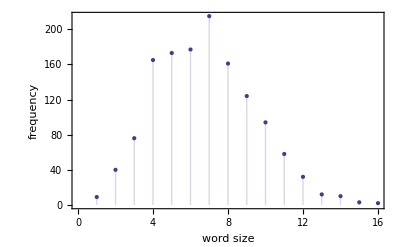

```mathematica
ListPlot[freq,Filling->Axis,Frame->True,FrameLabel->{Style["word size",12],Style["frequency",12]}]
```

We can also use the new Histogram command directly on the list of string lengths:

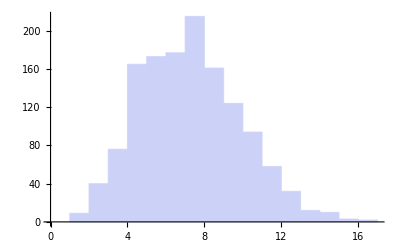

```mathematica
Histogram[StringLength[uniqueWords]]
```

For example, we can select to show only those words that have a frequency greater than some prescribed value. In the following code we extract words of frequency 20 or greater

```mathematica
Grid[Partition[Flatten[Select[Sort[Split[Sort[words]]/.{a___String}:>{First[{a}],Length[{a}]},#1[[2]]>#2[[2]]&],#[[2]]>19&]],6],Frame->All,Alignment->Left]
```

the | 662 | of | 494 | shall | 306
and | 258 | to | 184 | be | 179
or | 160 | in | 137 | States | 125
President | 121 | by | 100 | a | 94
United | 85 | for | 84 | any | 79
State | 77 | The | 64 | as | 64
have | 63 | Congress | 60 | such | 52
not | 44 | may | 44 | which | 43
from | 41 | on | 39 | all | 37
Vice | 36 | House | 32 | other | 31
this | 30 | Representatives | 29 | their | 28
Senate | 28 | one | 28 | Amendment | 28
he | 25 | Constitution | 25 | two | 24
that | 23 | Law | 23 | but | 23
at | 23 | thereof | 22 | Section | 22
each | 22 | No | 21 | no | 21
it | 21 | within | 20 | person | 20

Let us extract each occurrence of a key word from the text as well as its "surrounding word" so that the context of the word is made plain. By surrounding text we mean the keyword plus say n words on either side of the text, as illustrated below.

word1L word2L word3L … wordNL keyword word1R word2R word3R … wordNR

We will make use of a regular expression to achieve this goal. For example to search for "know":

"(\b\w+(?<!know)\W+?){6}\bknow\W+(?:(\w+(?<!know|knows))\W+){1,6}"

The explanation of the regular expression is given below

(						begin group 1
\b						word boundary
\w						any character
+						repeated one or more times
(?<!					begin negative lookback consisting of
know					the word "know"
)						close lookback group
\W						any non-character
+?						repeated one or more times (non gready)
)						close group 1
{6}						the proceeding is repeated exactly 6 times
\b						word boundary
know					the word "know"
\W						any non-character
+						repated one or more times
(?:						begin a non-looahead/lookback group
(						begin group 2
\w						any character
+						repeated  one or more times
(?<!					begin negative lookback consisting of
know|knows				the word know or knows
)						close lookback group
)						close group 2
)						close non-looahead/lookback group
\W						any non-character
+						repeated one or more times
{1,6}					the proceeding is repeated 1 or at most 6 times

```mathematica
Remove[Kwicfunc]
Kwicfunc[s_?StringQ,text_?StringQ]:=Module[{poslist},poslist=StringPosition[text,RegularExpression["(\\b\\w+(?<!"<>ToString[s]<>")\\W+?){6}\\b"<>ToString[s]<>"\\W+(?:(\\w+(?<!"<>ToString[s]<>"))\\W+){1,6}"]];
Grid[Map[{Style[StringReplace[StringTake[text,#],{"\n"->"",ToString[s]->Style[ToString[s],Red]}],9]}&,poslist],Alignment->Left,Frame->All]]
```

```mathematica
Kwicfunc["Senate",text]
```

States, which shall consist of a ~~Senate~~ and House of Representatives.Section 2
Power of Impeachment.Section 3The ~~Senate~~ of the United States shall be 
States shall be President of the ~~Senate~~, butshall have no Vote, unless 
unless they be equally divided.The ~~Senate~~ shall chuse their other Officers, and 
President of the United States.The ~~Senate~~ shall have the sole Power to 
the House of Representatives;but the ~~Senate~~ may propose or concur with Amendments 
the House of Representatives and the ~~Senate~~,shall, before it become a Law, 
to which the Concurrence of the ~~Senate~~ andHouse of Representatives may be 
repassed by two thirds of the ~~Senate~~ and House of Representatives, accordingto 
directed tothe President of the ~~Senate~~. The President of the 
shall, in the Presenceof the ~~Senate~~ and House of Representatives, open all 
more who have equal Votes, the ~~Senate~~ shall chuse fromthem by Ballot 
the Advice and Consent of the ~~Senate~~, to makeTreaties, provided two thirds 
the Advice and Consent of the ~~Senate~~, shall appointAmbassadors, other public Ministers 
happen duringthe Recess of the ~~Senate~~, by granting Commissions which shall expire 
of its equal Suffrage in the ~~Senate~~.Article VI.All Debts contracted and 
directed to the President ofthe ~~Senate~~;The President of the 
shall, in the presence of the ~~Senate~~ and House ofRepresentatives, open all 
highest numberson the list, the ~~Senate~~ shall choose the Vice-President; a 
census or enumeration.Amendment XVIIThe ~~Senate~~ of the United States shall be 
representation of any State in the ~~Senate~~, theexecutive authority of such State 
of the persons from whom the ~~Senate~~ may choose a Vice Presidentwhenever 
the President pro tempore of the ~~Senate~~and the Speaker of the House 
the President pro tempore of the ~~Senate~~ and the Speaker ofthe House 
the President pro tempore of the~~Senate~~ and the Speaker of the House 
the President pro tempore of the ~~Senate~~ and theSpeaker of the House

### Excercise

Create a list of 100 random integers between 1 and 1000 and extract all that are dividable by 
a) 7 or 5
b) neither 3 or 2
c) 2, 3 and 5

Create a list of 100 random integers between 1 and 10. Extract all elements except 5's.

Create your own symbolic sum function, including the common sum rules:

∑=∑_(i=1)^n 
∑(a_i+b_i) = ∑a_i+∑b_i
∑c a_i= c∑a_i
∑c= c n 
∑_(i=1)^m a_i+∑_(i=m+1)^n a_i=∑_(i=1)^n a_i, 1<m<n

Extend your sum function to include index shifts

∑_(i=1)^n a_i=∑_(i=x)^(n+x) a_(i-x)

Extend your sum function to include the special case

∑_(i=1)^n i=(n(n+1))/2

Can your sum function handle multiple sums:
∑_(j=1)^m ∑_(i=1)^n a_i b_j

Program solutions to the following problems; base the programs on pattern matching and the use of replacement rules. 
a) Given a list of elements (some of which may appear more than once), construct a list containing all (different) permutations of the elements. 
b) Given a list of the form {integer, nZeros}, for example, {23, 0, 0, 0, 0, 0}, construct all lists of integers a_i(i=1,…,n+1) (i.e., of the same length as the original list) with ∑_(i=1)^(n+1) a_i="integer" (i.e., which have the same sum as the original list). Put the a_i in increasing order: a_i≤a_(i+1),(i=1,…,n-1).

## Assignments

Required Reading:

Assignments
Making Definitions for Indexed Objects
Making Definitions for Functions
Immediate and Delayed Definitions
Special Forms of Assignment

### Set (=)

```mathematica
?=
```

RowBox[{StyleBox["lhs", "TI"], "=", StyleBox["rhs", "TI"]}] evaluates StyleBox["rhs", "TI"] and assigns the result to be the value of StyleBox["lhs", "TI"]. From then on, StyleBox["lhs", "TI"] is replaced by StyleBox["rhs", "TI"] whenever it appears. 
RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["l", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["l", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "=", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}] evaluates the SubscriptBox[StyleBox["r", "TI"], StyleBox["i", "TI"]], and assigns the results to be the values of the corresponding SubscriptBox[StyleBox["l", "TI"], StyleBox["i", "TI"]].

In its simplest usage, Set assigns a value to a variable:

```mathematica
a=1
b=2
a+b^3
a
Set[a,2];
a
Clear[a,b]; (* clear variables *)
```

1

2

9

1

2

The left hand side is not restricted to single characters:

```mathematica
VolumeOfUnitSphere=(4 π)/3 (* use meaningful variable names *)
Clear[VolumeOfUnitSphere]
```

(4 π)/3

One can also asign lists to a variable:

```mathematica
a={1,2,3,4,5,6,7,8};
a[[3]]         (* get the third element of a *)
{a,b,c,d}={1,2,3,4};  (* assign multiple values *)
c
{a,b,c,d}={a,c,b,d}; (* swap values *)
c
Clear[a,b,c,d];
```

3

3

2

Generally, anything can be assigned to anything:

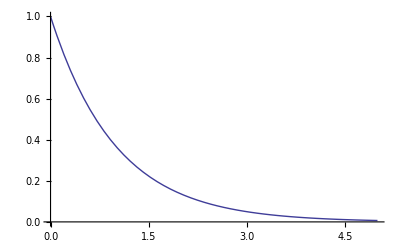
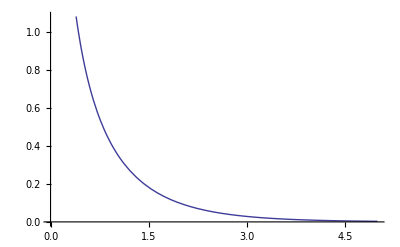

```mathematica
f=Plot[Exp[-t],{t,0,5}];
g=Plot[Exp[-t]/(√t),{t,0,5}];
f g
Clear[f,g]
```

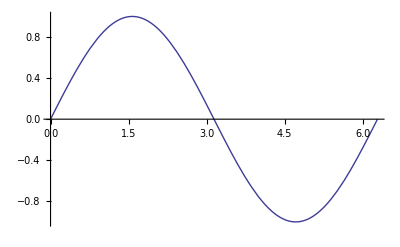

```mathematica
a=Plot;
a[Sin[x],{x,0,2 Pi}]
Clear[a];
```

```mathematica
t=TableForm[{{1,2,3,4,5,6,7,8,9,0},{a,b,c,d,e,f,g,h,i,j}},TableHeadings->Automatic];
t
Clear[t];
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 0
2 | a | b | c | d | e | f | g | h | i | j

Set is an immediate assignment. Say, we assign the value 2 to the symbol a (a=2). Now, whenever Mathematica meets the symbol a it immediately replaces it with its assigned value (2 in this case). Only then a calculation continues.
Example:

```mathematica
(a+b)^2
Integrate[x^2,{x,a,b}]
a=2;b=3;
(a+b)^2
Integrate[x^2,{x,a,b}]
Clear[a,b];
```

(a+b)^2

-a^3/3+b^3/3

25

19/3

### SetDelayed (:=)

```mathematica
?:=
```

RowBox[{StyleBox["lhs", "TI"], ":=", StyleBox["rhs", "TI"]}] assigns StyleBox["rhs", "TI"] to be the delayed value of StyleBox["lhs", "TI"]. StyleBox["rhs", "TI"] is maintained in an unevaluated form. When StyleBox["lhs", "TI"] appears, it is replaced by StyleBox["rhs", "TI"], evaluated afresh each time.

On a first glance SetDelayed works like Set:

```mathematica
a:=1
b:=2
a+b^3
a
Set[a,2];
a
Clear[a,b]; (* clear variables *)
```

9

1

2

The important difference is, that using a:= ... a remains enevaluated until it is used somewhere else. Why is this a difference? Take the following example, involving a random number generator:

```mathematica
?Random
```

RowBox[{"Random", "[", "]"}] gives a uniformly distributed pseudorandom Real in the range 0 to 1. 
RowBox[{"Random", "[", RowBox[{StyleBox["type", "TI"], ",", StyleBox["range", "TI"]}], "]"}] gives a pseudorandom number of the specified type, lying in the specified range. Possible types are: Integer, Real and Complex. The default range is 0 to 1. You can give the range RowBox[{"{", RowBox[{StyleBox["min", "TI"], ",", StyleBox["max", "TI"]}], "}"}] explicitly; a range specification of StyleBox["max", "TI"] is equivalent to RowBox[{"{", RowBox[{"0", ",", StyleBox["max", "TI"]}], "}"}].

```mathematica
r=Random[] (* this first executes the right hand side, i.e. creates a random number, and then assigns the result to the left hand side *)
```

0.681162

```mathematica
{r,r,r}
```

{0.681162,0.681162,0.681162}

Now we use SetDelayed

```mathematica
r:=Random[] (* the right hand side remains unevaluated, note that there is no semi-colon to supress output *)
```

```mathematica
{r,r,r}
```

{0.854217,0.432088,0.897439}

Now, r is evaluated each time it is used! We will meet SetDelayed later, when we create functions.

One possible application is to perform a calculation on demand and cache the result:

```mathematica
pi2:=pi2=N[Pi^2,50]
```

```mathematica
pi2
```

9.8696044010893586188344909998761511353136994072408

```mathematica
Definition[pi2]
```

pi2=9.8696044010893586188344909998761511353136994072408

```mathematica
Clear[pi2]
```

### Example: Programming the Fibonacci sequence

Dynamic programming for the Fibonacci sequence:

```mathematica
Clear[fib]
```

```mathematica
fib[1]=fib[2]=1;
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]
```

Note, that we chain f[x_]:=f[x]=.... this makes Mathematica remember f[x] which is especially important in iterative procedures. Sometimes, this might be unfeasible due to memory constraints. So far Mathematica does not know any Fibonacci number except 1.

```mathematica
Definition[fib]
```

fib[1]=1
 
fib[2]=1
 
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]

```mathematica
fib[5]
```

5

After computing fib[5], Mathematica knows and remembers the intermediary steps.

```mathematica
fib[240]//AbsoluteTiming
```

{0.,64202014863723094126901777428873111802307548623680}

Since Mathematica now knows fib[240], the repeated call takes no time.

```mathematica
fib[240]//AbsoluteTiming
```

{0.,64202014863723094126901777428873111802307548623680}

The next iteration step is also almost instantaneous, since all 240 steps before are cached.

```mathematica
fib[241]//AbsoluteTiming
```

{0.,103881042195729914708510518382775401680142036775841}

If we omit the immediate Set in the definition, Mathematica is going to nest the fib[ ] functions which leads to very large computation times and possible kernel freezes( crashes).

```mathematica
Clear[fib]
```

```mathematica
fib1[1]=fib1[2]=1;
fib1[n_]:=fib1[n-1]+fib1[n-2]
```

```mathematica
fib[1]=fib[2]=1;
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]
```

```mathematica
AbsoluteTiming[fib1[30]]
```

{1.9344,832040}

```mathematica
AbsoluteTiming[fib[30]]
```

{0.,832040}

```mathematica
Clear[fib,fib]
```

### Shortcuts

#### (Pre)Increment (++)

```mathematica
?Increment
```

RowBox[{StyleBox["x", "TI"], "++"}] increases the value of StyleBox["x", "TI"] by 1, returning the old value of StyleBox["x", "TI"].

```mathematica
k=1; k++
```

1

```mathematica
k
```

2

```mathematica
?PreIncrement
```

RowBox[{"++", StyleBox["x", "TI"]}] increases the value of StyleBox["x", "TI"] by 1, returning the new value of StyleBox["x", "TI"].

```mathematica
k=1; ++k
```

2

```mathematica
k
```

2

```mathematica
Clear[k]
```

#### (Pre)Decrement (--)

```mathematica
?Decrement
```

RowBox[{StyleBox["x", "TI"], "--"}] decreases the value of StyleBox["x", "TI"] by 1, returning the old value of StyleBox["x", "TI"].

```mathematica
k=1;k--
```

1

```mathematica
k
```

0

```mathematica
?PreDecrement
```

RowBox[{"--", StyleBox["x", "TI"]}] decreases the value of StyleBox["x", "TI"] by 1, returning the new value of StyleBox["x", "TI"].

```mathematica
k=1;--k
```

0

```mathematica
k
```

0

```mathematica
Clear[k]
```

#### AddTo, SubtractForm, TimesBy, DividedBy

```mathematica
?+=
```

RowBox[{StyleBox["x", "TI"], "+=", StyleBox["dx", "TI"]}] adds StyleBox["dx", "TI"] to StyleBox["x", "TI"] and returns the new value of StyleBox["x", "TI"].

```mathematica
k=1;k+=5
```

6

```mathematica
k
```

6

```mathematica
?-=
```

RowBox[{StyleBox["x", "TI"], "-=", StyleBox["dx", "TI"]}] subtracts StyleBox["dx", "TI"] from StyleBox["x", "TI"] and returns the new value of StyleBox["x", "TI"].

```mathematica
k=1;k-=5
```

-4

```mathematica
k
```

-4

```mathematica
?TimesBy
```

RowBox[{StyleBox["x", "TI"], "*=", StyleBox["c", "TI"]}] multiplies StyleBox["x", "TI"] by StyleBox["c", "TI"] and returns the new value of StyleBox["x", "TI"].

```mathematica
k=3;k*=5
```

15

```mathematica
k
```

15

```mathematica
?DivideBy
```

RowBox[{StyleBox["x", "TI"], "/=", StyleBox["c", "TI"]}] divides StyleBox["x", "TI"] by StyleBox["c", "TI"] and returns the new value of StyleBox["x", "TI"].

```mathematica
k=15;k/=3
```

5

```mathematica
k
```

5

```mathematica
Clear[k]
```

### Clearing Assignments

#### Unset

```mathematica
?=.
```

RowBox[{StyleBox["lhs", "TI"], "=."}] removes any rules defined for StyleBox["lhs", "TI"].

```mathematica
x=5;
x=.
x
```

x

#### Clear

```mathematica
?Clear
```

RowBox[{"Clear", "[", RowBox[{SubscriptBox[StyleBox["symbol", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["symbol", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] clears values and definitions for the SubscriptBox[StyleBox["symbol", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Clear", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_1\)\"", ShowStringCharacters->True], ",", StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_2\)\"", ShowStringCharacters->True], ",", StyleBox["…", "TR"]}], "]"}] clears values and definitions for all symbols whose names match any of the string patterns SubscriptBox[StyleBox["form", "TI"], StyleBox["i", "TI"]].

```mathematica
x=5
```

5

```mathematica
Clear[x]
```

#### ClearAll

```mathematica
?ClearAll
```

RowBox[{"ClearAll", "[", RowBox[{SubscriptBox[StyleBox["symb", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["symb", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] clears all values, definitions, attributes, messages and defaults associated with symbols. 
RowBox[{"ClearAll", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_1\)\"", ShowStringCharacters->True], ",", StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_2\)\"", ShowStringCharacters->True], ",", StyleBox["…", "TR"]}], "]"}] clears all symbols whose names textually match any of the SubscriptBox[StyleBox["form", "TI"], StyleBox["i", "TI"]].

We will omit ClearAll until we know a little more about functions and Attributes.

#### Remove

```mathematica
?Remove
```

RowBox[{"Remove", "[", RowBox[{SubscriptBox[StyleBox["symbol", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] removes symbols completely, so that their names are no longer recognized by StyleBox["Mathematica", FontSlant -> "Italic"]. 
RowBox[{"Remove", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_1\)\"", ShowStringCharacters->True], ",", StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_2\)\"", ShowStringCharacters->True], ",", StyleBox["…", "TR"]}], "]"}] removes all symbols whose names match any of the string patterns SubscriptBox[StyleBox["form", "TI"], StyleBox["i", "TI"]].

Later more on Remove

## Functions

Required Reading:

Defining Functions

### Very useless functions

One way to define a named function is to give any symbol an argument:

```mathematica
Clear[f,x];
f[x]=2 x^2- x + 1
```

1-x+2 x^2

```mathematica
f[x]
```

1-x+2 x^2

```mathematica
f[x]^2
```

(1-x+2 x^2)^2

But it turns out, that this definition is of limited use.

```mathematica
f[y]
```

f[y]

```mathematica
f[2]
```

f[2]

The reason is, that we provided a explicit definition for the expression f[x]!

```mathematica
?f
```

Global`f

f[x]=1-x+2 x^2

but we did not supply a definition for f[2] or f[y]. Mathematica evaluates expressions by matching patterns and does not automatically assume that f[2] or f[y] matches the pattern f[x].  In this sense, f[x] behaves more like a symbolic name than like a function; it is a symbol that masquerades as a function.

```mathematica
MatchQ[f[2],f[x]]
```

False

We could give independent definitions for other arguments of f

```mathematica
f[2]="The argument is 2"
```

The argument is 2

```mathematica
f[y]=Sin[y]
```

Sin[y]

The symbol f is now associated with a collection of assignments that may or may not be related.

```mathematica
?f
```

Global`f

f[2]=The argument is 2
 
f[x]=1-x+2 x^2
 
f[y]=Sin[y]

```mathematica
Clear[f]
```

### More useful examples

If we want Mathematica to recognize f[2] or f[y] as examples of a more general function f[x], we must define our function using a pattern argument, as follows.

```mathematica
Clear[g];
g[x_]=2 x^2- x + 1
```

1-x+2 x^2

The additional underscore attached to the argument x_ is used on the lhs to indicate that any expression can be used as the argument of this function and that the argument will be named x for the purpose of evaluating the rhs. In other words, x is a dummy argument.  However, the underscore is not used on the rhs — once the argument is given, it is referred to as x in the subsequent definition of the function.  With this version of the function, any argument is substituted for x_.

```mathematica
g[y]
```

1-y+2 y^2

```mathematica
g[2+123]
```

31126

```mathematica
g[4!]
```

1129

```mathematica
g[Log[x]]
```

1-Log[x]+2 Log[x]^2

```mathematica
g[a+b+c+d+e+f]
```

1-a-b-c-d-e-f+2 (a+b+c+d+e+f)^2

The pattern x_ matches any expression

```mathematica
MatchQ[2,x_]
```

True

```mathematica
MatchQ[2*Sin[x], x_]
```

True

#### Excercises

Create the function e^-x sin x using a pattern argument.

Write a function with two arbitrary arguments which returns the ratio between their difference and their sum as a percentage.  Be sure to test it!

Write a function which converts between Fahrenheit and Celsius temperature.  (Fahrenheit to Celsius: (Tf - 32)5/9 . The input should identify its scale and the output should be the other scale — in other words, the same function should operate in both directions depending upon the input presented.  [Hint : create a function with two arguments, a value and a unit.  The numerical value should be a dummy argument.  Two definitions of the function should be given for the cases where the unit is either Fahrenheit or Celsius.]  Be sure to test the function.  Verify that it is listable with respect to temperature.

### Even more useful function definitions

We already know that there are two different kinds of assignments in Mathematica.  lhs=rhs and lhs:=rhs. The basic difference between these forms is when the expression rhs is evaluated. lhs=rhs is an immediate assignment, in which rhs is evaluated at the time when the assignment is made. lhs:=rhs, on the other hand, is a delayed assignment, in which rhs is not evaluated when the assignment is made, but is instead evaluated each time the value of lhs is requested.

For example: we create a function that cast a six sided dice

```mathematica
Clear[dice]
dice=RandomInteger[{1,6}]
```

3

```mathematica
dice
```

3

```mathematica
dice
```

3

As you see, the function is not dicing. During the definition of the function the following happened:
We asked Mathematica to set lhs=rhs. The rhs was evaluated immediately and then the assignment took place. Lets look at another example. The Mathematica function Expand[expr] expands out products and positive integer powers in expr.

```mathematica
(a+b)^2
Expand[(a+b)^2]
```

(a+b)^2

a^2+2 a b+b^2

```mathematica
Expand[(1+x+y)(2-x)^3]
```

8-4 x-6 x^2+5 x^3-x^4+8 y-12 x y+6 x^2 y-x^3 y

Now we use it in a function definition

```mathematica
Clear[f,g,x];
g[x_] = Expand[x^2-1];
f[x_] := Expand[x^2-1]
```

Note the different coloring of x and the missing ; at the second assignment!

```mathematica
g[y]
```

-1+y^2

```mathematica
f[y]
```

-1+y^2

for more complex arguments, the different behavior becomes apparent:

```mathematica
g[x+y]
```

-1+(x+y)^2

```mathematica
f[x+y]
```

-1+x^2+2 x y+y^2

Take a look at the stored definitions:

```mathematica
?g
```

Global`g

g[x_]=-1+x^2

```mathematica
?f
```

Global`f

f[x_]:=Expand[x^2-1]

The difference arises from the evaluation schemes for the two functions.  Although we included Expand in the definition of g, it has no effect because rhs is evaluated immediately and is already expanded as much as its definition permits.  Thus, Expand no longer appears in the definition stored for g.

In most cases, SetDelayed is more appropriate if you want to define a function. Our dice example would look like

```mathematica
Clear[workingdice]
workingdice:=RandomInteger[{1,6}]
```

```mathematica
workingdice
workingdice
workingdice
```

4

1

1

A function without argument is of course of limited use. Let's upgrade our workingdice to allow for n casts

```mathematica
Clear[workingdice]
workingdice[n_]:=RandomInteger[{1,6},n]
```

```mathematica
workingdice[10]
```

{6,3,4,4,1,1,5,1,6,4}

#### Excercise

Define a function  that will compute the volume of a  sphere of radius r.

### Multiple Arguments

To set up a function that takes more than one argument you use a sequence of arguments. Let's enhance our workingdice to include non-six sided dice also.

```mathematica
workingdice[sides_,n_]:=RandomInteger[{1,sides},n]
```

```mathematica
workingdice[10,5]
```

{7,10,7,4,4}

```mathematica
workingdice[100,10]
```

{3,37,99,55,4,97,45,78,82,52}

Note, that we did not clear the prior definition!

```mathematica
?workingdice
```

Global`workingdice

workingdice[n_]:=RandomInteger[{1,6},n]
 
workingdice[sides_,n_]:=RandomInteger[{1,sides},n]

Both definitions are still active. Now we have a function that behaves differently, depening on how many arguments we provide:

```mathematica
workingdice[10]
```

{6,1,1,1,3,1,2,2,1,4}

```mathematica
workingdice[7,10]
```

{4,4,1,5,1,6,4,2,4,7}

In the section before, we learned to put constraints on arguments. We could, for example define a function that only works on lists. We could have defined our workingdice differently:

```mathematica
workingdice[{sides_,n_}]:=RandomInteger[{1,sides},n]
```

```mathematica
?workingdice
```

Global`workingdice

workingdice[{sides_,n_}]:=RandomInteger[{1,sides},n]
 
workingdice[n_]:=RandomInteger[{1,6},n]
 
workingdice[sides_,n_]:=RandomInteger[{1,sides},n]

```mathematica
workingdice[{4,4}]
```

{4,2,3,1}

#### Excercise:

Define a function (in a single line) that will compute the surface area of a right
circular cylinder of radius r and height h.

Define a function  that will compute the volume of a spherical shell of inner radius ri and outer radius ro.

### Lists as Arguments

It is also possible to construct a function such, that it takes whole lists as arguments. As an example we use a 3-dim vecotr as input:

```mathematica
Remove[function]
function[{x_,y_,z_}]:={-x,y,z}
```

```mathematica
function[{1,2,3}]
```

{-1,2,3}

If we don't want to refer to individual components we might also use different definitions

```mathematica
Remove[function]
function[x__]:=-x
```

```mathematica
function[{1,2,3}]
```

{-1,-2,-3}

Note, that the braces are now not in the argument definition! Compare with

```mathematica
Remove[function]
function[{x__}]:=-x
```

```mathematica
function[{1,2,3}]
```

-6

In the definition above, the x does not represent a list! It represents the sequence of list elements. This means that using x ca produce unexpected results.

The proper way to do it would be:

```mathematica
Remove[function]
function[{x__}]:=-{x}
```

```mathematica
function[{1,2,3}]
```

{-1,-2,-3}

#### Excercise

Define a function that takes a list as input and returns the length of the list.

Define a function that takes a vector as input and the vector in reverse order.

Define a function that takes a list as input and returns True if all elements are numbers.

Define a function that takes a list of characters as input and returns the joined string as output.

### Argument Selective Functions

We already learned that patterns may have restrictions. This allows us to create functions that are only working for certain arguments, or that have multiple definitions depending on which argument we suppy.

A function definition that will take any single argument:

```mathematica
Clear[f,g]
f[x_] := (x+1)^2
```

```mathematica
{f[1],f[a + b c]}
```

{4,(1+a+b c)^2}

A function definition for integer arguments only:

```mathematica
g[x_Integer] := Prime[x]-x
```

```mathematica
{g[10],g[z]}
```

{19,g[z]}

Make a definition with the condition that x should be positive:

```mathematica
Clear[g,f]
```

```mathematica
f[x_]:=ppp[x]/;x>0
```

```mathematica
f[5]
```

ppp[5]

```mathematica
f[-6]
```

f[-6]

This rule applies to any expression of the form w[x_,y_], with the added restriction that y==1-x.

```mathematica
w[x_,y_]:=p[x]/;y==1-x
```

```mathematica
w[4,-3]
```

p[4]

#### Excercise

Create a polynomial function of degree 3 that only accepts integer input.

Create a polynomial function of degree 3 that only accepts even integer input.

Create a sine function that only accepts input angles between 0 and π/2 (Mathematica expects the angles to be in radian).

Create a function that transforms a pair of Cartesian coordinates {x,y} to polar form{r,θ} using a quadrant - sensitive form of ArcTan that accepts two arguments.  Test your function on a list of points, such as {{1, 2}, {-2, -3}, {0, 1}, {-3, 0}}?  Define another function which performs the inverse transformation and test it also.

Define a function that will take a year such as 2008 and return True if it is a
leap year and False if it is not. (You’ll need to look up the exact definition of
leap years to do this!)

### When none of the patterns match & messages

Required reading:

Messages
Documentation Constructs

Usually we provide Mathematica with informations about what to do when the provided arguments match a given pattern.

```mathematica
Remove[myFunction]
myFunction[x_?NumericQ,y_?NumericQ]/;x<2y:=N[x+y]
```

```mathematica
myFunction[4,Pi]
```

7.14159

However, if we provide non-matching arguments Mathematica just returns the input unevaluated because we didn't tell it what to do

```mathematica
myFunction[9,4]
```

myFunction[9,4]

To catch function calls, we can provide a definition that matches 'everything' and use this to print out error messages for example.

In our case, this 'any input' would be [x_, y_]. Message[symbol::tag]prints the message symbol::tag unless it has been switched off.

```mathematica
Remove[myFunction]
myFunction[x_?NumericQ,y_?NumericQ]/;x<2y:=N[x+y]
myFunction[x_,y_]:=(Message[myFunction::badArgs];Null)
myFunction::badArgs="call with two numeric inputs";
```

```mathematica
myFunction[9,4]
```

myFunction::badArgs: call with two numeric inputs

It is also possible to insert the argument values into the error text: Message[symbol::tag,e_1,e_2,…]prints a message, inserting the values of the e_i as needed.

```mathematica
Remove[myFunction]
myFunction[x_?NumericQ,y_?NumericQ]/;x<2y:=N[x+y]
myFunction[x_,y_]:=(Message[myFunction::badArgs,x,y];Null)
myFunction::badArgs="call with two numeric inputs, violated condition: `1` < 2×`2`";
```

```mathematica
myFunction[9,4]
```

myFunction::badArgs: call with two numeric inputs, violated condition: 9 < 2×4

We might also want to catch cases, where the number of arguments is wrong

```mathematica
myFunction[9,]
```

myFunction::badArgs: call with two numeric inputs, violated condition: 9 < 2×Null

```mathematica
myFunction[9]
```

myFunction[9]

We could use __ to catch one or more arguments:

```mathematica
Remove[myFunction]
myFunction[x_?NumericQ,y_?NumericQ]/;x<2y:=N[x+y]
myFunction[x__]:=(Message[myFunction::badArgs,{x}];Null)
myFunction::badArgs="call with two numeric inputs, you entered `1`"
```

call with two numeric inputs, you entered `1`

```mathematica
myFunction[1,2,4]
```

myFunction::badArgs: call with two numeric inputs, you entered {1, 2, 4}

```mathematica
myFunction[9,4]
```

myFunction::badArgs: call with two numeric inputs, you entered {9, 4}

Hmm, actually we gave numeric arguments so the error message is misleading.

To be more specific we add another message

```mathematica
Remove[myFunction]
myFunction[x_?NumericQ,y_?NumericQ]/;x<2y:=N[x+y]
myFunction[x_?NumericQ,y_?NumericQ]/;x≥2y:=(Message[myFunction::badArgs,x,y];Null)
myFunction[x__]:=(Message[myFunction::argx,{x}];Null)
myFunction::badArgs="`1` needs to be smaller than 2×`2`";
myFunction::argx="call with two numeric inputs, you entered `1`";
```

```mathematica
myFunction[1,2,4]
```

myFunction::argx: call with two numeric inputs, you entered {1, 2, 4}

```mathematica
myFunction[9,4]
```

myFunction::badArgs: 9 needs to be smaller than 2×4

But two blanks don't match nothing

```mathematica
myFunction[]
```

myFunction[]

but three Blanks will

```mathematica
Remove[myFunction]
myFunction[x_?NumericQ,y_?NumericQ]/;x<2y:=N[x+y]
myFunction[x_?NumericQ,y_?NumericQ]/;x≥2y:=(Message[myFunction::badArgs,x,y];Null)
(* here are now three blanks instead of 2 *)
myFunction[x___]:=(Message[myFunction::argx,{x}];Null)
myFunction::badArgs="`1` needs to be smaller than 2×`2`";
myFunction::argx="call with two numeric inputs, you entered `1`";
```

```mathematica
myFunction[]
```

myFunction::argx: call with two numeric inputs, you entered {}

Finally we will provide our function with an usage explanation

```mathematica
myFunction::usage="myFunction[x,y] calculates the sum x+y if x < 2y."
```

myFunction[x,y] calculates the sum x+y if x < 2y.

```mathematica
?myFunction
```

myFunction[x,y] calculates the sum x+y if x < 2y.

It is also possible to define syntax information to activate syntax highlighting for our function.

```mathematica
SyntaxInformation[myFunction]={"ArgumentsPattern"->{_,_}};
```

```mathematica
{myFunction[],myFunction[x],myFunction[x,y],myFunction[x,y,z],myFunction[x,y,z,w]};
```

myFunction::argx: call with two numeric inputs, you entered {}

myFunction::argx: call with two numeric inputs, you entered {x}

myFunction::argx: call with two numeric inputs, you entered {x, y}

General::stop: Further output of myFunction will be suppressed during this calculation.

```mathematica
Remove[myFunction]
```

### Postfix, Prefix, Infix

Mathematica offers a variety of ways to apply a function to an argument. The standard form is to append the argument in squared brackets appended to the function name:

```mathematica
function[argument]
```

function[argument]

```mathematica
Sin[2 Pi]
```

0

One problem is, that a an argument can again be the function of an argument. You can easily nest many levels of expressions. This makes it sometimes difficult to keep track of opened/closed brackets.

```mathematica
f[f[f[f[f[f[f[x]]]]]]]
```

f[f[f[f[f[f[f[x]]]]]]]

Mathematica tried to assist with interactive syntax highlighting, but the whole expression is still difficult to read and disentangle.

```mathematica
Simplify[Expand[Integrate[x^2+3 x^4-x+2 √x-Log[x],x]]]
```

x+(4 x^(3/2))/3-x^2/2+x^3/3+(3 x^5)/5-x Log[x]

Instead ot enclosing the argument in brackets, you can also use the postfix form, given a function that only depends on a single arguement

```mathematica
f[x]===x//f
```

f[False]

```mathematica
Simplify[(Sin[x]^2-Tan[x]^2)/Cosh[x]^2]===(Sin[x]^2-Tan[x]^2)/Cosh[x]^2//Simplify
```

False

```mathematica
TableForm[Table[{i,i^2,i^3,i^4,i^5},{i,1,10}]]
```

1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125
6 | 36 | 216 | 1296 | 7776
7 | 49 | 343 | 2401 | 16807
8 | 64 | 512 | 4096 | 32768
9 | 81 | 729 | 6561 | 59049
10 | 100 | 1000 | 10000 | 100000

```mathematica
Table[{i,i^2,i^3,i^4,i^5},{i,1,10}]//TableForm
```

1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125
6 | 36 | 216 | 1296 | 7776
7 | 49 | 343 | 2401 | 16807
8 | 64 | 512 | 4096 | 32768
9 | 81 | 729 | 6561 | 59049
10 | 100 | 1000 | 10000 | 100000

Another nice way of writing a function is the Prefix form

```mathematica
f[x]===f@x
```

True

This is especially handy, if you want to apply a function to a lengthy argument, because there is no need to scroll to the end of the expression to close the brackets.

```mathematica
Sort@RandomInteger[1000,100]
```

{14,45,64,67,81,89,95,97,103,108,109,135,149,154,169,184,186,186,198,209,215,222,225,232,233,244,269,280,283,294,305,316,322,322,325,332,334,335,338,339,369,382,415,425,448,450,453,454,456,458,462,480,485,494,496,501,514,524,530,541,548,574,578,585,589,589,590,622,623,629,634,636,638,652,656,679,695,697,727,759,765,768,797,798,843,867,889,890,905,910,914,925,967,973,978,981,984,985,993,997}

The Pre- and Postfix form can be combined and also used in a chain

```mathematica
f@g@h@x
```

f[g[h[x]]]

```mathematica
h@x//g//f
```

f[g[h[x]]]

The Infix form can be used with functions of several variables

Infix[f[e_1,e_2,…]] prints with f[e_1,e_2,…] given in default infix form: e_1~f~e_2~f~e_3….

```mathematica
x~f~y
```

f[x,y]

```mathematica
Infix[head[a,b,c,d]]
```

a ~head~ b ~head~ c ~head~ d

```mathematica
Postfix[f[x]]
Prefix[f[x+y]]
```

x//f

f@(x+y)

```mathematica
N@Cos@45
Cos[45] //N
```

0.525322

0.525322

#### Excercise

The Prefix and Infix forms can only be used when the function you want to apply works with a single argument. Give an example of a Post/Prefix application with functions of two or more arguments

Create a 5x5 matrix using the Table command and assign it to a variable. Show the matrix in TableForm, MatrixForm and as Grid, using the Postfix formalism

### Pure Functions

Required Reading:

Pure Functions
Variables in Pure Functions and Rules

If you define a function using the standard assignment f[arg_]:=some_definition you create a function and give it a name (namely f). In some circumstances it is not necessary to give an assignment particular name because e.g. you only need it once. This can be done using Function[x,body], which defines a a pure function in which x is replaced by any argument you provide.

```mathematica
Function[x,1+2 x +x^2]
```

Function[x,1+2 x+x^2]

To apply this function to a variable use any of the discussed ways (Postfix, Infix, Prefix, ....

```mathematica
Function[x,1+2 x +x^2][y]
```

1+2 y+y^2

```mathematica
Function[x,1+2 x +x^2]@y
```

1+2 y+y^2

```mathematica
y//Function[x,1+2 x +x^2]
```

1+2 y+y^2

Giving this Function a name is equivalent to our standard function definition

```mathematica
f=Function[x,1+2 x +x^2];
```

```mathematica
f[10]
```

121

```mathematica
f@10
```

121

Practically there is no need to explicitely name the arguments either. The shorthand notation for Function is (function of #)&

```mathematica
Function[x,1+2 x +x^2]
```

Function[x,1+2 x+x^2]

```mathematica
(1+2#+#^2)&
```

1+2 #1+#1^2&

```mathematica
(1+2#+#^2)&[y]
```

1+2 y+y^2

# represents the first argument supplied to a pure function. #n represents the n-th argument. Hence a pure function of several arguments looks like:

```mathematica
Function[{x,y},x^2+y^2]
```

Function[{x,y},x^2+y^2]

```mathematica
(#1^2+#2^2)&
```

#1^2+#2^2&

Pure functions in Mathematica can take any number of arguments. You can use ## to stand for all the arguments that are given, and ##n to stand for the n^th and subsequent arguments.

##  stands for all arguments.

```mathematica
f[##, ##] &[x, y]
```

1+2 x+x^2

##2 stands for all arguments except the first one

```mathematica
f[##2,#1]&[a,b,c,ap,bp]
```

1+2 b+b^2

Pure functions fully shine when we encounter Mathematica commands like Apply, Map, Thread, etc.

Pure functions can also be used to use the postfix form with functions of more than one parameter.

Imagine a given list which we want to Flatten only at level 1 using the postfix form.

```mathematica
Clear[list]
list={a,b,{{c,c,c}},d,{1,2,3,4{a1,a2},5},{{{{aef1,aef3}}}},e,f}
```

{a,b,{{c,c,c}},d,{1,2,3,{4 a1,4 a2},5},{{{{aef1,aef3}}}},e,Function[x,1+2 x+x^2]}

Using the single-argument form of Flatten, gets rid of all sub-levels

```mathematica
list//Flatten
```

{a,b,c,c,c,d,1,2,3,4 a1,4 a2,5,aef1,aef3,e,Function[x,1+2 x+x^2]}

But we can set up a pure function to provide Flatten with the level argument:

```mathematica
list//Flatten[#,1]&
```

{a,b,{c,c,c},d,1,2,3,{4 a1,4 a2},5,{{{aef1,aef3}}},e,Function[x,1+2 x+x^2]}

```mathematica
Clear[list]
```

#### Excercise

Create a linear pure function and calculate the result for a few arguments.

Create a pure functional polynomial of degree 3 and calculate it for a few arguments

Create the pure function pendant of f[x_, y_] := xy + x Sqrt[x + y]-y^2

Create a pure function that takes a list as argument and returns the second element.

Create a pure function that takes a vector as argument and returns its norm.

Create a pure function that takes two vectors of the same dimension as arguments and returns their scalar product. Create asecond pure function that returns the vector product.

### Example: Law of cosines example

Taken from Thomas H. Meyer, Department of Natural Resources and the Environment
University of Connecticut thomas.meyer@uconn.edu

#### Law of cosines example

This is a somewhat more complicated, and probably more useful, example based on the planar law of cosines:
cos[θ]==(a^2+b^2-c^2)/(2a b)

In "practice," the LOC can reasonably be used given the angle and two sides from which the third side is to be found, or given three sides from which the angle is to be found. Let's write a single function to do all of that.

This definition automatically determines that we're looking for the angle given three sides

```mathematica
LOC[θ_Symbol,a_?NumericQ,b_?NumericQ,c_?NumericQ]:=ArcCos[(a^2+b^2-c^2)/(2a b)]
```

```mathematica
LOC[α,50,60,70.]/°
```

78.463

This definition automatically determines that we're looking for the side opposite the angle given the adjacent sides and the angle

```mathematica
LOC[θ_?NumericQ,a_?NumericQ,b_?NumericQ,c_Symbol]:=√(-2a b Cos[θ]+b^2+a^2)
```

```mathematica
LOC[78.463°,60,70.,c]
```

82.5833

We can do the algebra for all four cases, but Mathematica solve the equation for us

```mathematica
Remove[LOC]
LOC[θ_Symbol,a_?NumericQ,b_?NumericQ,c_?NumericQ]:=Solve[Cos[θ]==(a^2+b^2-c^2)/(2a b),θ]
LOC[θ_?NumericQ,a_Symbol,b_?NumericQ,c_?NumericQ]:=Solve[Cos[θ]==(a^2+b^2-c^2)/(2a b),a]
LOC[θ_?NumericQ,a_?NumericQ,b_Symbol,c_?NumericQ]:=Solve[Cos[θ]==(a^2+b^2-c^2)/(2a b),b]
LOC[θ_?NumericQ,a_?NumericQ,b_?NumericQ,c_Symbol]:=Solve[Cos[θ]==(a^2+b^2-c^2)/(2a b),c]
```

```mathematica
LOC[α,50,60,70.]
LOC[78.463°,60,70.,c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→-1.36944},{α→1.36944}}

{{c→-82.5833},{c→82.5833}}

This is cool, but the rules and the negative roots are annoying. Also, let's use a single function rather than repeat the Solve four times

```mathematica
Remove[LOC]
LOCBase[θ_,a_,b_,c_,var_Symbol]:=Max[var/.Solve[Cos[θ]==(a^2+b^2-c^2)/(2a b),var]]

LOC[θ_Symbol,a_?NumericQ,b_?NumericQ,c_?NumericQ]:=LOCBase[θ,a,b,c,θ]
LOC[θ_?NumericQ,a_Symbol,b_?NumericQ,c_?NumericQ]:=LOCBase[θ,a,b,c,a]
LOC[θ_?NumericQ,a_?NumericQ,b_Symbol,c_?NumericQ]:=LOCBase[θ,a,b,c,b]
LOC[θ_?NumericQ,a_?NumericQ,b_?NumericQ,c_Symbol]:=LOCBase[θ,a,b,c,c]
```

```mathematica
LOC[α,50,60,70.]
LOC[78.463°,a,50.,50]
LOC[78.463°,60,b,70.]
LOC[78.463°,60,70.,c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.36944

20.0001

50.0001

82.5833

One last refinement: have Mathematica find the symbol for us. The braces around var take care of Select always returning a list.

```mathematica
Remove[LOC]
LOCBase[θ_,a_,b_,c_,{var_Symbol}]:=Max[var/.Solve[Cos[θ]==(a^2+b^2-c^2)/(2a b),var]]

LOC[θ_,a_,b_,c_]:=LOCBase[θ,a,b,c,Select[{θ,a,b,c},Head[#]===Symbol&]]
```

```mathematica
LOC[α,50,60,70.]
LOC[78.463°,a,50.,50]
LOC[78.463°,60,b,70.]
LOC[78.463°,60,70.,c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.36944

20.0001

50.0001

82.5833

### Excercises

#### Reverse integer

Write and test a function whose effect upon an integer is to reverse its digits.  For example, the input 123 should produce output 321.  Be sure to account for the sign.

#### Apocalyptic numbers

In numerology, a number of the form 2^n that contains the beast number 666 among its sequence of decimal digits is known as an apocalyptic number.  Write a simple procedure that lists the first m exponents that generate apocalyptic numbers.  What are the first 10 apocalyptic numbers?

#### Making change

Write a function that determines the number of coins of each domination needed to provide a specified amount of change using the smallest number of coins.  The output should be a list of pairs containing the number of coins and its denomination.  For example, the change for 0.87 would be {{3,0.25},{1,0.1},{0,0.05},{2,0.01}}.  Begin with standard U.S. denominations, namely, {0.25,0.1,0.05,0.01}, and then generalize to an arbitrary list of denominations.